# The distribution of amino acid changes in different species

Analysis and comparison of A=to-I RNA editing in cephalopod species (squids and octopuses) and humans.

Zhamilya Bilyalova, Jun. 24,  2018

## Introduction: What is RNA editing?

RNA editing is a process that changes a RNA transcript such that it would no longer correspond to a sequence of DNA in a genome. There are many types of changes. A-to-I RNA editing is widespread in animals and results in the modification of a adenosine to inosine which will be read as a guanine. Nucleotides are being changed by enzymes that catalyze the editing.

Nucleobases that participate in A-to-I editing in mRNA:

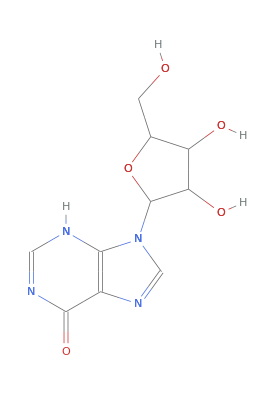
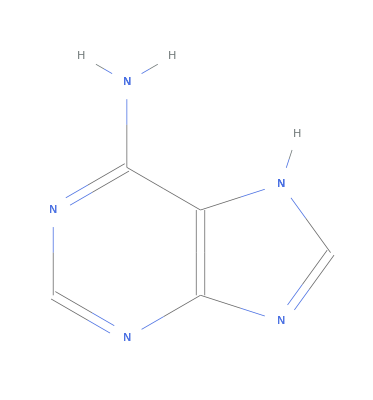
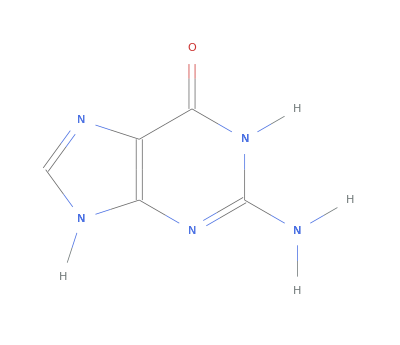
-Graphics-Inosine | -Graphics-Adenine | -Graphics-Guanine

```mathematica
Grid[{Map[Labeled[ChemicalData[#],#,Left]&,{"Inosine","Adenine","Guanine"}]},Spacings->2]
```

A-to-I editing in messenger RNA (mRNA) can cause changes in the amino acid sequence of a protein (amino acid recoding). Codons, 64 combinations in total, are codes for specific amino acids (one amino acid can relate to more than one codon).

To find what codons correspond to a specific amino acid, we can implement this code: An example is given for amino acid glycine:

```mathematica
Entity["Chemical","Glycine"][EntityProperty["Chemical","Codons"]]
```

{GGU,GGC,GGA,GGG}

Properties of a specific amino acid:

```mathematica
Entity["Chemical","Glycine"]["Properties"];
```

And this is a table of amino acids and their corresponding codons:

```mathematica
Grid[Map[{#,#[EntityProperty["Chemical","Codons"]]}&,Interpreter["Chemical"][{"Ser","Gly","Cys","Phe","Leu","Tyr","tryptophan","Arg","histidine","Gln","Pro","Ile","Met","Val","Ala","Asn","Lys","Asp","Glu"}]],Frame->All]
```

L-serine | {UCU,UCC,UCA,UCG,AGU,AGC}
glycine | {GGU,GGC,GGA,GGG}
L-cysteine | {UGU,UGC}
L-phenylalanine | {UUU,UUC}
L-leucine | {UUA,UUG,CUU,CUC,CUA,CUG}
L-tyrosine | {UAU,UAC}
L-tryptophan | {UGG}
L-arginine | {CGU,CGC,CGA,CGG,AGA,AGG}
L-histidine | {CAU,CAC}
L-glutamine | {CAA,CAG}
L-proline | {CCU,CCC,CCA,CCG}
L-isoleucine | {AUU,AUC,AUA}
L-methionine | {AUG}
L-valine | {GUU,GUC,GUA,GUG}
L-alanine | {GCU,GCC,GCA,GCG}
L-asparagine | {AAU,AAC}
L-lysine | {AAA,AAG}
L-aspartic acid | {GAU,GAC}
L-glutamic acid | {GAA,GAG}

## Goal of this essay and description of the data

It was recently discovered that RNA editing and amino acid changes are widespread in cephalopods (octopus and squid). In this essay, I attempt to analyse and compare the distribution of amino acid changes in cephalopod species and human.

The data set consists of calculated expected distribution ("Expected amount", "Expected frequency") and observed distribution ("Edits", "Frequency") of amino acid changes in humans, four cephalopod species, and conserved edits from those species. KR  represents a change from amino acid K to amino acid R. "syn" means synonymous, does not make any changes to amino acid and is likely to not have an effect. "stop_W" means stop to w and causes a significant change in a protein sequence.

### Data

```mathematica
data=SemanticImport@URLDownload["https://github.com/ZhamilyaB/Summer2018Starter/raw/master/editingcodonsimplifieddata.xlsx"]
```

Dataset[<>]

```mathematica
datagrouped=data[GroupBy["Species"]]
```

Dataset[<>]

All types of amino acids changes are categorized as either radical or conserved. Radical changes are those that change the physicochemical property of the amino acid while conservative changes do not. The ratio of radical to conservative changes indicates how many changes are likely to have a negative effect.

```mathematica
radcon=Dataset[{
<|"Change"->"YC","A"->"R","B"->"R","C"-> "R"|>,<|"Change"->"TA","A"->"C","B"->"C","C"-> "C"|>,
<|"Change"->"syn","A"->"","B"->"","C"-> ""|>,<|"Change"->"SG","A"->"C","B"->"C","C"-> "C"|>,
<|"Change"->"RG","A"->"R","B"->"R","C"-> "R"|>,<|"Change"->"QR","A"->"C","B"->"R","C"-> "R"|>,
<|"Change"->"pW","A"->"","B"->"","C"-> ""|>,<|"Change"->"NS","A"->"C","B"->"R","C"-> "C"|>,
<|"Change"->"ND","A"->"R","B"->"C","C"-> "R"|>,<|"Change"->"MV","A"->"C","B"->"C","C"-> "C"|>,
<|"Change"->"KR","A"->"C","B"->"C","C"-> "C"|>,<|"Change"->"KE","A"->"R","B"->"R","C"-> "R"|>,
<|"Change"->"IV","A"->"C","B"->"C","C"-> "C"|>,<|"Change"->"IM","A"->"C","B"->"C","C"-> "C"|>,
<|"Change"->"HR","A"->"C","B"->"C","C"-> "C"|>,<|"Change"->"EG","A"->"R","B"->"R","C"-> "R"|>,
<|"Change"->"DG","A"->"R","B"->"R","C"-> "R"|>}]
```

Dataset[<>]

### Assumptions

Amino acid changes also can be random or non-random:  Random edits are likely to be slightly bad and don’t make an animal better, Non-random edits are likely to be good, be actively preserved in the population and seen more in conserved. In humans most changes are random, therefore, they are most likely to have a negative effect. In Individual cephalopod species, amino acid changes are a lot less random and they are less likely to have a negative effect. In conserved, changes are least random  and most likely to have a positive effect.

## Visualisation and Exploration

#### Expected frequency vs. actual frequency

```mathematica
coloredAmino=<|"KR"->RGBColor[0.010563313554859288, 0.842598209242611, 0.28387676305890275],"SG"->RGBColor[0.27953532144977733, 0.4836435395506147, 0.42893085600422864],"IM"->RGBColor[0.550447550119203, 0.1376882171135425, 0.10417086466364123],"TA"->RGBColor[0.5007397164248966, 0.7840482366236328, 0.7045968561167071],"IV"->RGBColor[0.2073047547900564, 0.09766618304217212, 0.7900750170440545],"MV"->RGBColor[0.7368627516800415, 0.9854810528894713, 0.16876607015856604],"HR"->RGBColor[0.6257486253643563, 0.18583347602533107, 0.08319093382232734],"NS"->RGBColor[0.9619547743747547, 0.5741162790544341, 0.1898822938015785],"ND"->RGBColor[0.2786813860224029, 0.8446411358513435, 0.5682812147647314],"QR"->RGBColor[0.7161778051845769, 0.7079120059790731, 0.8547544010382961],"KE"->RGBColor[0.9204697991268052, 0.01247026853391442, 0.588547608246031],"EG"->RGBColor[0.5494103924690645, 0.28378601201396725, 0.9354421828064061],"RG"->RGBColor[0.7039543181525214, 0.4665112553665334, 0.9831352427359885],"YC"->RGBColor[0.5185946438295199, 0.3923872911409534, 0.20838843032037646],"DG"->RGBColor[0.965242919857114, 0.6592751425902181, 0.052085256107477385],"stop-W"->RGBColor[0.5034569251580197, 0.09809664422436004, 0.7443255369657586]|>; (*Assigning colors to the types of amino acid changes for better visualization*)
```

```mathematica
legend=SwatchLegend[Values@coloredAmino,Keys@coloredAmino,LegendLabel->"Aminoacids changes",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5]
```

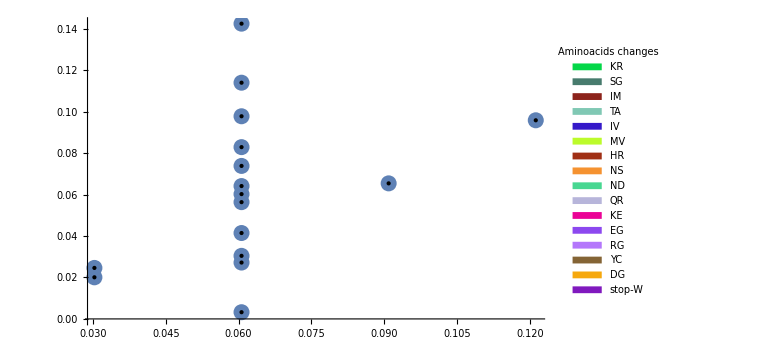
-Graphics-FrequencyExpected Frequency

```mathematica
Labeled[ListPlot[
MapThread[Style[#1,Values[#2]]&,{Values@Normal[datagrouped[["human",All,{"Expected_frequency","Frequency"}]]],Normal@coloredAmino}],
PlotLegends->legend,
PlotStyle->PointSize[0.02],
ImageSize->Large],{Style["Frequency",Bold],Style["Expected Frequency",Bold]},{Left, Bottom}, RotateLabel->True]
```

Cephalopod species:

```mathematica
coloredAmino2=<|"KR"->RGBColor[0.010563313554859288, 0.842598209242611, 0.28387676305890275],"SG"->RGBColor[0.27953532144977733, 0.4836435395506147, 0.42893085600422864],"IM"->RGBColor[0.550447550119203, 0.1376882171135425, 0.10417086466364123],"TA"->RGBColor[0.5007397164248966, 0.7840482366236328, 0.7045968561167071],"IV"->RGBColor[0.2073047547900564, 0.09766618304217212, 0.7900750170440545],"syn"-> Black,"MV"->RGBColor[0.7368627516800415, 0.9854810528894713, 0.16876607015856604],"HR"->RGBColor[0.6257486253643563, 0.18583347602533107, 0.08319093382232734],"NS"->RGBColor[0.9619547743747547, 0.5741162790544341, 0.1898822938015785],"ND"->RGBColor[0.2786813860224029, 0.8446411358513435, 0.5682812147647314],"QR"->RGBColor[0.7161778051845769, 0.7079120059790731, 0.8547544010382961],"KE"->RGBColor[0.9204697991268052, 0.01247026853391442, 0.588547608246031],"EG"->RGBColor[0.5494103924690645, 0.28378601201396725, 0.9354421828064061],"RG"->RGBColor[0.7039543181525214, 0.4665112553665334, 0.9831352427359885],"YC"->RGBColor[0.5185946438295199, 0.3923872911409534, 0.20838843032037646],"DG"->RGBColor[0.965242919857114, 0.6592751425902181, 0.052085256107477385],"stop-W"->RGBColor[0.5034569251580197, 0.09809664422436004, 0.7443255369657586]|>; (*Assigning colors to the types of amino acid changes for better visualization*)
```

```mathematica
legend2=SwatchLegend[Values@coloredAmino2,Keys@coloredAmino2,LegendLabel->"Aminoacids changes",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5];
```

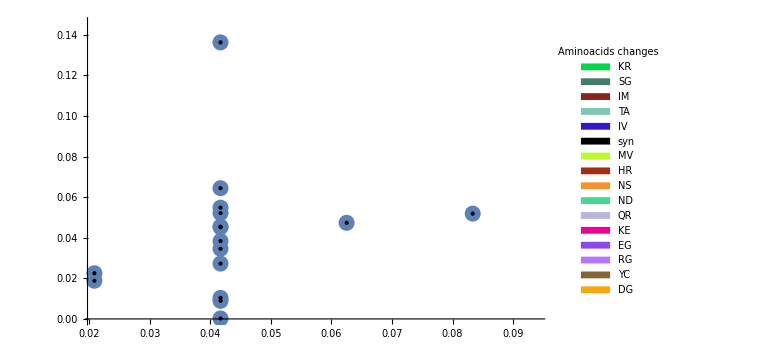
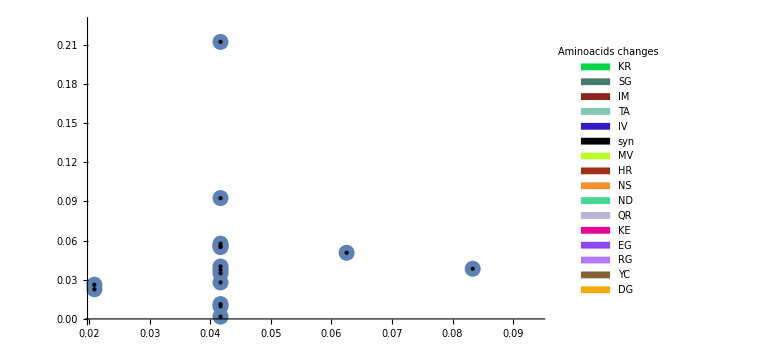
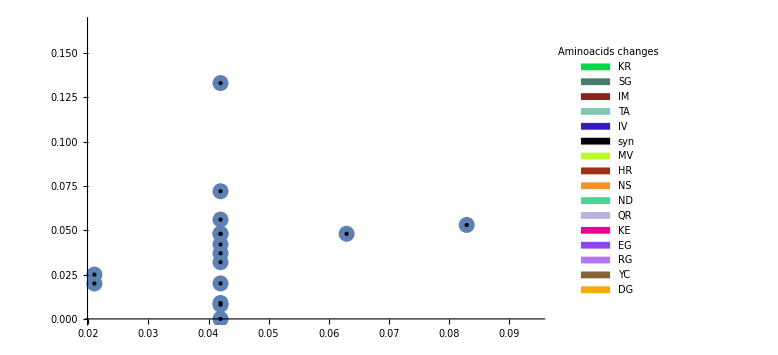
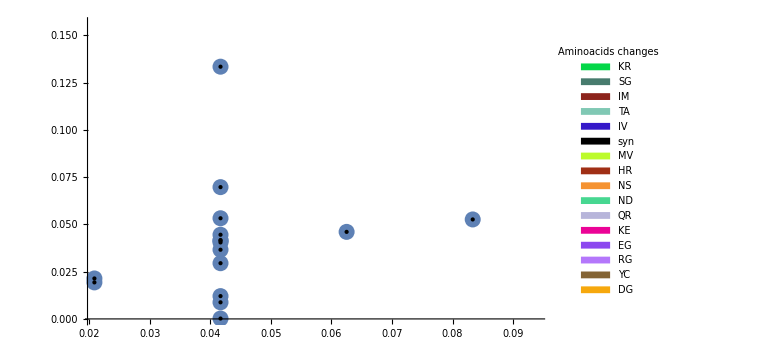
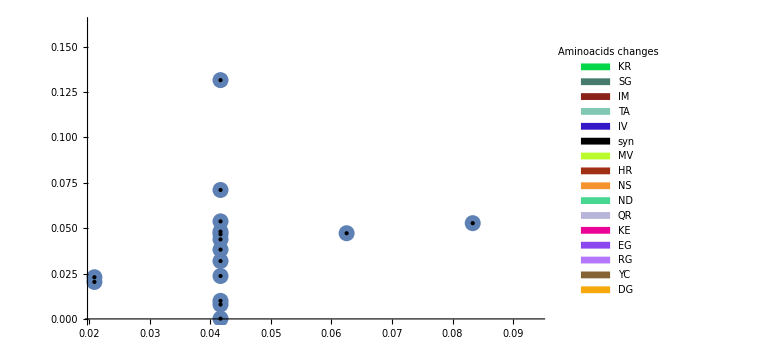
{-Graphics-FrequencyExpected Frequency,-Graphics-FrequencyExpected Frequency,-Graphics-FrequencyExpected Frequency,-Graphics-FrequencyExpected Frequency,-Graphics-FrequencyExpected Frequency}

```mathematica
Table[Labeled[ListPlot[
MapThread[Style[#1,Values[#2]]&,{Values@Normal[datagrouped[[species,All,{"Expected_frequency","Frequency"}]]],Normal@coloredAmino2}],
PlotLegends->legend2,
PlotStyle->PointSize[0.02],
ImageSize->Large],{Style["Frequency",Bold],Style["Expected Frequency",Bold]},{Left, Bottom}, RotateLabel->True],
{species,{"specific_sepia","conserved_cephalopods","specific_oct_bim","specific_squid","specific_oct_vul"}}]
```

#### The comparison of frequencies of changes in all species

With this plot we are trying to explore the amino acid changes that are

1) the most different and the most similar  in all of the species.

2) how and why are they different or similar?

3) and what is the general pattern?

```mathematica
rulesTicks=MapIndexed[#1->First[#2]&,{"KR","SG","IM","TA","IV","MV","HR","NS","ND","QR","KE","EG","RG","YC","DG","stop-W","syn"}]
```

{KR→1,SG→2,IM→3,TA→4,IV→5,MV→6,HR→7,NS→8,ND→9,QR→10,KE→11,EG→12,RG→13,YC→14,DG→15,stop-W→16,syn→17}

```mathematica
rulesColors={_String->Blue}
```

{_String→RGBColor[0, 0, 1]}

```mathematica
rules=Join[rulesTicks,rulesColors]
```

{KR→1,SG→2,IM→3,TA→4,IV→5,MV→6,HR→7,NS→8,ND→9,QR→10,KE→11,EG→12,RG→13,YC→14,DG→15,stop-W→16,syn→17,_String→RGBColor[0, 0, 1]}

```mathematica
Labeled[ListPlot[
MapThread[Style[{#2,#1},#3]&,Transpose@Values[Normal[data[All,{"Change","Frequency","Species"}]]]/.rules],
Ticks->{Automatic,Transpose@{Values[rulesTicks],Keys[rulesTicks]}},
ImageSize->Large],{"Changes","Frequency"},{Left, Bottom}, RotateLabel->True]
```

Values::invrl: The argument … is not a valid Association or a list of rules.

MapThread::list: List expected at position 2 in ….

Values::invrl: The argument … is not a valid Association or a list of rules.

General::stop: Further output of Values::invrl will be suppressed during this calculation.

MapThread::list: List expected at position 2 in ….

General::stop: Further output of MapThread::list will be suppressed during this calculation.

ListPlot::lpn: … is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[MapThread[Style[{#2,#1},#3]&,Transpose[Values[{{0.173256,0.299507}→1,{0.253463,0.308773}→1,{0.273401,0.260426}→1,{0.0320262,0.477867}→1,{0.268563,0.448904}→1,{0.110742,0.323099}→1,{0.157943,0.337264}→1,{0.31514,0.331593}→1,{0.236364,0.557469}→1,{0.247437,0.551722}→1,{0.136465,0.384382}→1,{0.210162,0.492779}→1,{0.0657911,0.465294}→1,{0.140753,0.649608}→1,{0.148734,0.538346}→1,{0.273218,0.683328}→1,{0.14696,0.504658}→1,{0.124375,0.677911}→1,{0.212416,0.725033}→1,{0.321997,0.666953}→1,{0.199945,0.62034}→1,{0.160525,0.750479}→1,{0.399018,0.496912}→1,{0.416379,0.704201}→1,{0.410358,0.781591}→1,{0.273133,0.737512}→1,{0.392654,0.738828}→1,{0.312651,0.575747}→1,{0.439721,0.740896}→1,{0.439614,0.778862}→1,{0.374852,0.598489}→1,{0.258974,0.57134}→1,{0.272267,0.65821}→1,{0.454782,0.563377}→1,{0.214959,0.770826}→1,{0.282878,0.691639}→1,{0.301723,0.723443}→1,{0.438876,0.634808}→1,{0.430864,0.864734}→1,{0.536423,0.727544}→1,{0.398285,0.65579}→1,{0.518897,0.719618}→1,{0.381182,0.827752}→1,{0.418432,0.60891}→1,{0.324383,0.696559}→1,{0.472884,0.722223}→1,{0.509939,0.783216}→1,{0.610006,0.874371}→1,{0.495414,0.651605}→1,{0.449091,0.794689}→1,{0.517653,0.634199}→1,{0.56455,0.770047}→1,{0.591948,0.866123}→1,{0.594633,0.738629}→1,{0.433068,0.822065}→1,{0.515959,0.7356}→1,{0.453099,0.760823}→1,{0.478016,0.859028}→1,{0.469859,0.769102}→1,{0.69618,0.678154}→1,{0.457376,0.784275}→1,{0.667643,0.853115}→1,{0.744269,0.867676}→1,{0.532736,0.859526}→1,{0.620247,0.765721}→1,{0.781412,0.667606}→1,{0.545381,0.715507}→1,{0.747315,0.82758}→1,{0.617504,0.684944}→1,{0.63883,0.926717}→1,{0.845927,0.700767}→1,{0.770368,0.747635}→1,{0.663881,0.91247}→1,{0.643694,0.761075}→1,{0.701792,0.761008}→1,{0.785625,0.769408}→1,{0.647423,0.863745}→1,{0.632722,0.690699}→1,{0.732112,0.744261}→1,{0.786064,0.775916}→1,{0.843963,0.885161}→1,{0.910656,0.639468}→1,{0.909503,0.643991}→1,{0.846055,0.879127}→1,{0.768547,0.737103}→1,{0.966943,0.860964}→1,{0.849332,0.861765}→1,{0.930304,0.885249}→1,{0.913866,0.742917}→1,{1.01546,0.675986}→1,{0.834246,0.861}→1,{0.766597,0.728941}→1,{0.983399,0.84124}→1,{0.905528,0.676461}→1,{0.948097,0.820258}→1,{1.04138,0.657584}→1,{1.06065,0.672295}→1,{0.972265,0.688507}→1,{0.908635,0.612243}→1,{1.00808,0.833314}→1,{0.888205,0.722755}→1,{1.1225,0.533165}→1,{0.905923,0.569583}→1,{0.966585,0.621862}→1,{1.00889,0.797603}→1,{0.90799,0.534537}→1,{0.993689,0.720475}→1,{0.991294,0.550969}→1,{1.11328,0.719617}→1,{1.0485,0.712549}→1,{1.17596,0.695358}→1,{1.22965,0.590454}→1,{1.10504,0.653955}→1,{1.15556,0.636729}→1,{1.07733,0.492297}→1,{1.16354,0.432522}→1,{1.06012,0.46876}→1,{1.26917,0.541988}→1,{1.05302,0.508457}→1,{1.30414,0.487621}→1,{1.19966,0.44537}→1,{1.28345,0.590038}→1,{1.22899,0.422203}→1,{1.17847,0.606675}→1,{1.15009,0.558756}→1,{1.31801,0.584772}→1,{1.27747,0.379829}→1,{1.25411,0.401725}→1,{1.37855,0.50222}→1,{1.13126,0.474185}→1,{1.23104,0.526929}→1,{1.223,0.325216}→1,{1.35646,0.515879}→1,{1.27426,0.456383}→1,{1.36791,0.320363}→1,{1.34094,0.437821}→1,{1.34536,0.500539}→1,{1.31915,0.445832}→1,{1.32483,0.235559}→1,{1.27153,0.318371}→1,{1.41568,0.38549}→1,{1.30732,0.411573}→1,{1.3001,0.40518}→1,{1.21991,0.205931}→1,{1.4286,0.184568}→1,{1.38761,0.427901}→1,{1.46483,0.17287}→1,{1.33779,0.128089}→1,{1.37829,0.103082}→1,{1.31632,0.279835}→1,{1.33226,0.258497}→1,{1.2804,0.091197}→1,{1.28889,0.324234}→1,{1.47625,0.0394197}→1,{1.51788,0.0266584}→1,{1.52703,0.0477031}→1,{1.4251,0.0875635}→1,{1.45813,0.0930513}→1,{1.28262,0.198187}→1,{1.36067,0.153781}→1,{1.50319,0.00316866}→1,{1.27126,0.0688047}→1,{1.49079,0.104973}→1,{1.51763,0.125421}→1,{1.33978,0.133526}→1,{1.54476,0.181613}→1,{1.43454,0.129397}→1,{1.37348,0.124059}→1,{1.46434,-0.0987965}→1,{1.4119,-0.0396169}→1,{1.40308,0.019714}→1,{1.32887,-0.177272}→1,{1.36112,-0.156333}→1,{1.37576,-0.0629623}→1,{1.41392,-0.057018}→1,{1.53252,-0.0173051}→1,{1.33248,0.0110123}→1,{1.56652,-0.221505}→1,{1.56028,-0.212309}→1,{1.56366,-0.0207999}→1,{1.55253,-0.172341}→1,{1.37375,-0.230115}→1,{1.43595,-0.239341}→1,{1.40814,-0.096496}→1,{1.584,-0.348464}→1,{1.41249,-0.121453}→1,{1.5812,-0.199856}→1,{1.53289,-0.124309}→1,{1.59271,-0.411698}→1,{1.41371,-0.353454}→1,{1.5663,-0.336122}→1,{1.55605,-0.198889}→1,{1.33879,-0.260612}→1,{1.40014,-0.477588}→1,{1.41261,-0.404958}→1,{1.39976,-0.34155}→1,{1.54306,-0.343749}→1,{1.50417,-0.474304}→1,{1.4974,-0.554738}→1,{1.45695,-0.462062}→1,{1.35248,-0.421646}→1,{1.35892,-0.55835}→1,{1.49142,-0.458476}→1,{1.34801,-0.528866}→1,{1.31457,-0.459487}→1,{1.44675,-0.502619}→1,{1.3513,-0.46057}→1,{1.28009,-0.558795}→1,{1.37806,-0.481073}→1,{1.32741,-0.635511}→1,{1.4654,-0.583978}→1,{1.26652,-0.67483}→1,{1.51758,-0.748728}→1,{1.28972,-0.682264}→1,{1.50609,-0.774577}→1,{1.22422,-0.732972}→1,{1.37562,-0.826148}→1,{1.44687,-0.576038}→1,{1.39691,-0.600413}→1,{1.33486,-0.592934}→1,{1.37239,-0.597095}→1,{1.34956,-0.708903}→1,{1.18659,-0.677632}→1,{1.46219,-0.825204}→1,{1.33002,-0.898821}→1,{1.26056,-0.796855}→1,{1.34564,-0.699919}→1,{1.16724,-0.807118}→1,{1.28159,-0.71991}→1,{1.21568,-0.823836}→1,{1.40204,-0.773518}→1,{1.19296,-0.743848}→1,{1.35799,-0.944978}→1,{1.39729,-1.02115}→1,{1.32229,-0.927029}→1,{1.25049,-0.85637}→1,{1.23243,-0.834704}→1,{1.16986,-0.842871}→1,{1.07688,-1.10696}→1,{1.16611,-1.03526}→1,{1.13966,-1.06596}→1,{1.16731,-1.13345}→1,{1.21855,-1.17118}→1,{1.27658,-1.00738}→1,{1.08142,-1.05111}→1,{1.17855,-1.19587}→1,{1.25241,-1.1793}→1,{1.19643,-1.20902}→1,{1.07035,-1.24374}→1,{1.03884,-0.993248}→1,{1.15561,-1.203}→1,{1.09625,-0.999584}→1,{0.969495,-1.22249}→1,{1.18226,-1.293}→1,{1.0947,-1.21966}→1,{1.17158,-1.26886}→1,{0.883863,-1.30974}→1,{1.13756,-1.31312}→1,{0.958184,-1.30656}→1,{0.83327,-1.12568}→1,{1.01576,-1.2604}→1,{0.849248,-1.38106}→1,{1.00894,-1.21474}→1,{1.0293,-1.21598}→1,{0.809486,-1.24878}→1,{0.994867,-1.22835}→1,{0.986006,-1.29428}→1,{0.954752,-1.25145}→1,{0.762366,-1.22605}→1,{0.82168,-1.42851}→1,{0.717473,-1.23838}→1,{0.788547,-1.46919}→1,{0.754028,-1.21535}→1,{0.716919,-1.4312}→1,{0.640569,-1.38945}→1,{0.850462,-1.45488}→1,{0.848757,-1.29475}→1,{0.690406,-1.36856}→1,{0.64233,-1.55964}→1,{0.857074,-1.29247}→1,{0.769157,-1.44914}→1,{0.534067,-1.33791}→1,{0.732362,-1.38875}→1,{0.742337,-1.41111}→1,{0.739486,-1.32639}→1,{0.769445,-1.34239}→1,{0.699797,-1.41365}→1,{0.529858,-1.5292}→1,{0.552982,-1.35595}→1,{0.437365,-1.41931}→1,{0.392382,-1.48944}→1,{0.387563,-1.52958}→1,{0.467021,-1.63185}→1,{0.473167,-1.49261}→1,{0.44198,-1.38879}→1,{0.457589,-1.63654}→1,{0.572126,-1.55869}→1,{0.459891,-1.62054}→1,{0.483883,-1.66869}→1,{0.542648,-1.50954}→1,{0.292049,-1.51368}→1,{0.244501,-1.5883}→1,{0.482971,-1.48527}→1,{0.233381,-1.54698}→1,{0.169899,-1.58189}→1,{0.17035,-1.5012}→1,{0.136108,-1.60433}→1,{0.182693,-1.55757}→1,{0.380288,-1.73841}→1,{0.199332,-1.53553}→1,{0.269674,-1.67864}→1,{0.0867548,-1.71557}→1,{0.307653,-1.48682}→1,{0.0894148,-1.55505}→1,{0.125981,-1.50496}→1,{-0.00793013,-1.70687}→1,{0.0858921,-1.60417}→1,{0.0000391833,-1.66583}→1,{0.0861994,-1.65864}→1,{0.12353,-1.74554}→1,{0.125859,-1.70667}→1,{0.0141898,-1.63457}→1,{-0.10164,-1.77391}→1,{-0.108646,-1.50351}→1,{-0.173323,-1.50902}→1,{-0.0393101,-1.70145}→1,{-0.129547,-1.5191}→1,{-0.0593685,-1.74794}→1,{-0.186138,-1.65667}→1,{-0.0539434,-1.62115}→1,{-0.28344,-1.77664}→1,{-0.201565,-1.77183}→1,{-0.262856,-1.63075}→1,{-0.352477,-1.50563}→1,{-0.14376,-1.74114}→1,{-0.105372,-1.64704}→1,{-0.317761,-1.60113}→1,{-0.229487,-1.65839}→1,{-0.171295,-1.64511}→1,{-0.411057,-1.49393}→1,{-0.368653,-1.66729}→1,{-0.398808,-1.49623}→1,{-0.259327,-1.51829}→1,{-0.285829,-1.73501}→1,{-0.497797,-1.68382}→1,{-0.573918,-1.70636}→1,{-0.31376,-1.57371}→1,{-0.452777,-1.66708}→1,{-0.482632,-1.54872}→1,{-0.551593,-1.59803}→1,{-0.434145,-1.73722}→1,{-0.473146,-1.6054}→1,{-0.482859,-1.475}→1,{-0.656781,-1.52347}→1,{-0.573898,-1.64945}→1,{-0.522003,-1.7239}→1,{-0.631573,-1.51207}→1,{-0.746328,-1.48735}→1,{-0.796382,-1.69099}→1,{-0.544713,-1.57999}→1,{-0.675283,-1.45247}→1,{-0.748165,-1.56201}→1,{-0.607546,-1.39577}→1,{-0.783156,-1.44184}→1,{-0.699853,-1.49601}→1,{-0.946955,-1.41209}→1,{-0.768639,-1.47566}→1,{-0.719117,-1.43766}→1,{-0.903584,-1.53038}→1,{-0.885209,-1.60255}→1,{-0.886367,-1.51999}→1,{-0.760847,-1.44441}→1,{-0.787159,-1.5409}→1,{-0.970254,-1.59452}→1,{-0.876801,-1.43536}→1,{-1.05203,-1.4263}→1,{-1.10686,-1.27913}→1,{-0.9832,-1.39238}→1,{-0.92846,-1.54839}→1,{-1.02896,-1.49739}→1,{-1.17612,-1.25763}→1,{-1.1583,-1.50375}→1,{-0.954769,-1.45944}→1,{-1.20581,-1.26766}→1,{-1.24669,-1.43642}→1,{-1.10337,-1.35101}→1,{-1.21679,-1.33297}→1,{-1.25294,-1.2968}→1,{-1.29901,-1.2516}→1,{-1.27112,-1.2508}→1,{-1.14968,-1.20405}→1,{-1.32535,-1.27725}→1,{-1.2117,-1.36599}→1,{-1.15608,-1.19557}→1,{-1.3619,-1.32666}→1,{-1.34619,-1.07224}→1,{-1.44082,-1.33535}→1,{-1.29926,-1.23228}→1,{-1.4705,-1.07621}→1,{-1.3392,-1.28583}→1,{-1.33476,-1.17137}→1,{-1.261,-1.227}→1,{-1.30023,-1.10157}→1,{-1.30657,-1.12802}→1,{-1.57388,-1.03411}→1,{-1.42136,-1.05457}→1,{-1.40643,-0.918733}→1,{-1.49452,-1.08525}→1,{-1.52017,-1.09448}→1,{-1.39056,-1.03776}→1,{-1.37608,-1.08534}→1,{-1.65684,-1.03082}→1,{-1.61928,-1.01472}→1,{-1.65901,-1.07429}→1,{-1.55384,-0.786278}→1,{-1.72314,-1.06258}→1,{-1.47583,-1.01963}→1,{-1.55073,-0.946651}→1,{-1.68227,-0.911267}→1,{-1.54462,-0.791242}→1,{-1.63874,-0.698612}→1,{-1.69324,-0.790607}→1,{-1.77906,-0.79837}→1,{-1.54291,-0.790798}→1,{-1.823,-0.868212}→1,{-1.59388,-0.692306}→1,{-1.66998,-0.874893}→1,{-1.67842,-0.648247}→1,{-1.82036,-0.745977}→1,{-1.73454,-0.597885}→1,{-1.70248,-0.583878}→1,{-1.79609,-0.498488}→1,{-1.90656,-0.650139}→1,{-1.92541,-0.705712}→1,{-1.68668,-0.684986}→1,{-1.87127,-0.542928}→1,{-1.86616,-0.657046}→1,{-1.97694,-0.456877}→1,{-1.68842,-0.650913}→1,{-1.93861,-0.545596}→1,{-1.98557,-0.345418}→1,{-1.7341,-0.432465}→1,{-1.9503,-0.369444}→1,{-1.75838,-0.367091}→1,{-1.79194,-0.353903}→1,{-2.02274,-0.426025}→1,{-2.03497,-0.433718}→1,{-2.0348,-0.469031}→1,{-1.93827,-0.178341}→1,{-1.85005,-0.273416}→1,{-1.91166,-0.144644}→1,{-2.05892,-0.157316}→1,{-1.88111,-0.0990261}→1,{-2.00197,-0.315459}→1,{-1.91025,-0.235819}→1,{-2.09552,-0.188227}→1,{-2.09033,-0.226534}→1,{-2.00761,-0.0764615}→1,{-1.85108,-0.099485}→1,{-1.85216,-0.039668}→1,{-1.86927,-0.0817084}→1,{-1.84114,-0.101472}→1,{-1.86179,-0.123437}→1,{-1.94903,-0.0147033}→1,{-1.94791,-0.0343926}→1,{-1.87485,0.0739443}→1,{-2.1216,-0.0803207}→1,{-2.0316,0.105637}→1,{-1.98646,-0.0153516}→1,{-2.02884,-0.00613933}→1,{-2.10508,0.110028}→1,{-2.02993,0.0498573}→1,{-1.88576,0.313523}→1,{-2.1247,0.161744}→1,{-2.16891,0.2203}→1,{-2.11152,0.23319}→1,{-1.98885,0.138849}→1,{-2.10656,0.422562}→1,{-1.9989,0.29302}→1,{-1.93565,0.393269}→1,{-2.11013,0.393108}→1,{-2.15695,0.24066}→1,{-2.11172,0.439643}→1,{-2.15604,0.429957}→1,{-1.96803,0.436325}→1,{-2.09319,0.603218}→1,{-1.97537,0.566565}→1,{-2.03945,0.594787}→1,{-2.0203,0.618651}→1,{-1.91756,0.438187}→1,{-1.92946,0.497423}→1,{-2.11119,0.505145}→1,{-1.93797,0.61984}→1,{-2.13952,0.685392}→1,{-2.0673,0.792118}→1,{-2.05251,0.810854}→1,{-2.14476,0.622583}→1,{-1.94303,0.74616}→1,{-1.97088,0.783116}→1,{-2.04578,0.872324}→1,{-1.88085,0.847052}→1,{-1.95389,0.962621}→1,{-1.94011,0.991246}→1,{-1.88629,0.75414}→1,{-2.06147,0.783114}→1,{-2.05272,0.889835}→1,{-1.94066,0.967918}→1,{-1.87405,0.877149}→1,{-1.99385,0.90629}→1,{-1.93374,1.08161}→1,{-1.96946,0.971199}→1,{-1.8896,0.925475}→1,{-1.99353,1.20129}→1,{-1.93603,0.999603}→1,{-1.94471,1.16007}→1,{-2.00438,1.23051}→1,{-1.8366,1.01223}→1,{-1.747,1.07429}→1,{-1.81217,1.33114}→1,{-1.87655,1.2056}→1,{-1.90735,1.20494}→1,{-1.90895,1.19881}→1,{-1.96577,1.22022}→1,{-1.86414,1.16344}→1,{-1.82958,1.44495}→1,{-1.82893,1.22304}→1,{-1.7857,1.21916}→1,{-1.69542,1.46484}→1,{-1.90015,1.41001}→1,{-1.83448,1.39822}→1,{-1.66659,1.31735}→1,{-1.61841,1.59352}→1,{-1.74408,1.47561}→1,{-1.83294,1.56573}→1,{-1.76792,1.42504}→1,{-1.83425,1.66333}→1,{-1.71318,1.42661}→1,{-1.60133,1.60221}→1,{-1.73139,1.72554}→1,{-1.7208,1.6998}→1,{-1.49792,1.74377}→1,{-1.54238,1.64717}→1,{-1.59378,1.5622}→1,{-1.62603,1.73555}→1,{-1.46375,1.7757}→1,{-1.56624,1.73569}→1,{-1.44932,1.63572}→1,{-1.63472,1.84386}→1,{-1.47292,1.86237}→1,{-1.57624,1.9332}→1,{-1.35017,1.87302}→1,{-1.53469,1.82276}→1,{-1.3648,1.7869}→1,{-1.5166,1.75425}→1,{-1.42625,1.99931}→1,{-1.5022,1.90975}→1,{-1.26513,1.99632}→1,{-1.25558,1.85382}→1,{-1.28919,2.0708}→1,{-1.28255,2.0129}→1,{-1.30987,2.13852}→1,{-1.41726,2.04539}→1,{-1.23693,2.04666}→1,{-1.14345,1.9705}→1,{-1.35558,2.04754}→1,{-1.37449,2.16652}→1,{-1.265,1.99419}→1,{-1.12165,2.16799}→1,{-1.05137,2.20262}→1,{-1.2845,2.15003}→1,{-1.13784,2.26018}→1,{-1.18935,2.17823}→1,{-1.07453,2.21535}→1,{-1.1088,2.11415}→1,{-0.965619,2.35545}→1,{-1.03354,2.16742}→1,{-1.07912,2.27242}→1,{-0.945465,2.24301}→1,{-0.939539,2.30958}→1,{-0.925506,2.34084}→1,{-1.08418,2.43841}→1,{-0.831348,2.42573}→1,{-0.818331,2.46131}→1,{-0.945247,2.41348}→1,{-0.81665,2.25864}→1,{-0.790054,2.32627}→1,{-0.871496,2.28918}→1,{-0.78066,2.37537}→1,{-0.852497,2.50279}→1,{-0.795645,2.29123}→1,{-0.804649,2.37641}→1,{-0.709322,2.48525}→1,{-0.727122,2.4788}→1,{-0.567576,2.45688}→1,{-0.535145,2.38619}→1,{-0.735626,2.56427}→1,{-0.697993,2.58358}→1,{-0.683883,2.42863}→1,{-0.585917,2.40918}→1,{-0.505813,2.56614}→1,{-0.474933,2.60113}→1,{-0.544779,2.4252}→1,{-0.414793,2.47814}→1,{-0.506945,2.57176}→1,{-0.314459,2.68125}→1,{-0.532379,2.53726}→1,{-0.438993,2.42697}→1,{-0.251758,2.56274}→1,{-0.192619,2.68175}→1,{-0.330279,2.59218}→1,{-0.28754,2.70018}→1,{-0.300595,2.68571}→1,{-0.376961,2.58812}→1,{-0.128413,2.46613}→1,{-0.15946,2.68926}→1,{-0.0949224,2.59421}→1,{-0.184363,2.75015}→1,{-0.134197,2.74259}→1,{-0.0318824,2.71155}→1,{-0.195036,2.74949}→1,{-0.145141,2.50664}→1,{0.0930481,2.76256}→1,{-0.0460909,2.76121}→1,{0.0802189,2.5456}→1,{0.210584,2.50047}→1,{0.0274964,2.51887}→1,{0.2045,2.76366}→1,{0.216324,2.68833}→1,{0.0248036,-0.0307536}→2,{0.262371,0.141643}→2,{0.26043,-0.116242}→2,{0.212559,-0.00872574}→2,{0.13825,-0.0836684}→2,{0.130431,-0.159407}→2,{0.182645,-0.254337}→2,{0.0209268,-0.156188}→2,{0.103256,-0.00312348}→2,{0.0342045,-0.0241309}→2,{0.111055,-0.276656}→2,{0.102481,-0.13941}→2,{0.231121,-0.0626985}→2,{0.0891167,-0.253627}→2,{-0.049245,-0.0980947}→2,{0.0439075,-0.116824}→2,{0.0823194,-0.294463}→2,{0.129453,-0.320244}→2,{-0.0310674,-0.387276}→2,{-0.0431848,-0.369009}→2,{0.0936671,-0.31312}→2,{0.123648,-0.234857}→2,{0.0828875,-0.280616}→2,{0.176525,-0.452107}→2,{-0.0954527,-0.387881}→2,{-0.0532599,-0.439029}→2,{-0.0218629,-0.321906}→2,{-0.0044602,-0.419582}→2,{0.128426,-0.503094}→2,{-0.0812374,-0.459333}→2,{-0.130069,-0.502682}→2,{0.0895375,-0.455248}→2,{0.0452866,-0.299731}→2,{-0.173889,-0.485007}→2,{0.0338868,-0.475958}→2,{-0.00229061,-0.436997}→2,{-0.104368,-0.332329}→2,{-0.220487,-0.511148}→2,{-0.185967,-0.326809}→2,{-0.181782,-0.401289}→2,{-0.240385,-0.543608}→2,{-0.211383,-0.42825}→2,{-0.143332,-0.572156}→2,{-0.204742,-0.499}→2,{-0.0778398,-0.409837}→2,{-0.130882,-0.563269}→2,{-0.19662,-0.471759}→2,{-0.21316,-0.495104}→2,{-0.237585,-0.600398}→2,{-0.326595,-0.472847}→2,{-0.23317,-0.323467}→2,{-0.188946,-0.427733}→2,{-0.259706,-0.517843}→2,{-0.257911,-0.529189}→2,{-0.290095,-0.363408}→2,{-0.123778,-0.517429}→2,{-0.239767,-0.37919}→2,{-0.29994,-0.47226}→2,{-0.182285,-0.541339}→2,{-0.409418,-0.415527}→2,{-0.21252,-0.381608}→2,{-0.30796,-0.409889}→2,{-0.199286,-0.579045}→2,{-0.190144,-0.633686}→2,{-0.382984,-0.416282}→2,{-0.400106,-0.547999}→2,{-0.316083,-0.390807}→2,{-0.290385,-0.461688}→2,{-0.252098,-0.573051}→2,{-0.535918,-0.491676}→2,{-0.447871,-0.517752}→2,{-0.327727,-0.541682}→2,{-0.541713,-0.397265}→2,{-0.389491,-0.529504}→2,{-0.587217,-0.381995}→2,{-0.395472,-0.37796}→2,{-0.475125,-0.512363}→2,{-0.398047,-0.348989}→2,{-0.461073,-0.58461}→2,{-0.358065,-0.461773}→2,{-0.55407,-0.435703}→2,{-0.516314,-0.377385}→2,{-0.507224,-0.397932}→2,{-0.575658,-0.381071}→2,{-0.491715,-0.338346}→2,{-0.596272,-0.49673}→2,{-0.421706,-0.576826}→2,{-0.500157,-0.553147}→2,{-0.609876,-0.347193}→2,{-0.668698,-0.296031}→2,{-0.648057,-0.404204}→2,{-0.63216,-0.497164}→2,{-0.723618,-0.488429}→2,{-0.523152,-0.311929}→2,{-0.67618,-0.325336}→2,{-0.677753,-0.488715}→2,{-0.513283,-0.517814}→2,{-0.552062,-0.381225}→2,{-0.796325,-0.528259}→2,{-0.681019,-0.30257}→2,{-0.690245,-0.34785}→2,{-0.682459,-0.376666}→2,{-0.61088,-0.489843}→2,{-0.765925,-0.398061}→2,{-0.724792,-0.312249}→2,{-0.604726,-0.457032}→2,{-0.704145,-0.259036}→2,{-0.657634,-0.194347}→2,{-0.80943,-0.250862}→2,{-0.771718,-0.40676}→2,{-0.870331,-0.303857}→2,{-0.861374,-0.271921}→2,{-0.877823,-0.261045}→2,{-0.95309,-0.388831}→2,{-0.919667,-0.1901}→2,{-0.940515,-0.264355}→2,{-0.709537,-0.417341}→2,{-0.867243,-0.316294}→2,{-0.71796,-0.310943}→2,{-0.826156,-0.127368}→2,{-0.935157,-0.383868}→2,{-1.00708,-0.116606}→2,{-1.01322,-0.274008}→2,{-0.848665,-0.311757}→2,{-1.04973,-0.163936}→2,{-0.905771,-0.0811232}→2,{-0.963254,-0.316027}→2,{-0.88296,-0.225169}→2,{-1.06321,-0.0293869}→2,{-0.871407,-0.211287}→2,{-0.902362,-0.105284}→2,{-1.0358,-0.223617}→2,{-0.977734,-0.104077}→2,{-0.909395,-0.10154}→2,{-0.981635,0.0270504}→2,{-0.964155,-0.183936}→2,{-1.07049,-0.0759561}→2,{-0.908334,-0.0568854}→2,{-1.14508,-0.078141}→2,{-1.15245,-0.120799}→2,{-1.02758,0.0405968}→2,{-1.13624,0.0760538}→2,{-0.953754,0.0256399}→2,{-1.06759,0.115258}→2,{-0.904915,0.0130277}→2,{-1.08421,-0.00708213}→2,{-1.14901,0.101595}→2,{-1.20546,-0.0814363}→2,{-1.09651,0.0512919}→2,{-1.08273,0.189329}→2,{-1.16799,0.212879}→2,{-1.11943,0.0408768}→2,{-1.03789,0.211841}→2,{-1.23631,0.0617087}→2,{-1.05686,0.0370506}→2,{-0.953079,0.105733}→2,{-1.07382,0.0888961}→2,{-1.20654,0.0629086}→2,{-1.25994,0.118876}→2,{-1.24736,0.0768364}→2,{-1.22835,0.213913}→2,{-1.17114,0.0733331}→2,{-1.1683,0.307779}→2,{-1.10939,0.124728}→2,{-1.01304,0.139081}→2,{-1.20539,0.213581}→2,{-1.16568,0.350555}→2,{-1.04726,0.329775}→2,{-1.17673,0.34273}→2,{-1.13206,0.27239}→2,{-1.10104,0.220928}→2,{-1.23996,0.20093}→2,{-1.06414,0.266658}→2,{-1.24763,0.418022}→2,{-1.26896,0.44889}→2,{-1.01394,0.523654}→2,{-1.05452,0.443527}→2,{-1.28786,0.41079}→2,{-1.29958,0.397323}→2,{-1.20233,0.46778}→2,{-1.26945,0.503207}→2,{-1.11417,0.479415}→2,{-1.15967,0.481272}→2,{-1.19955,0.486394}→2,{-1.06322,0.515795}→2,{-1.10003,0.584435}→2,{-1.30356,0.40321}→2,{-1.13999,0.441842}→2,{-1.07909,0.565011}→2,{-1.1237,0.529846}→2,{-1.14157,0.505494}→2,{-1.1971,0.654378}→2,{-1.2893,0.618029}→2,{-1.28673,0.628365}→2,{-1.13961,0.659038}→2,{-1.01363,0.759959}→2,{-1.20781,0.633249}→2,{-1.25855,0.76706}→2,{-1.08262,0.658781}→2,{-1.07918,0.865324}→2,{-1.08003,0.893527}→2,{-1.26876,0.788518}→2,{-1.22365,0.756545}→2,{-1.23309,0.936552}→2,{-1.17435,0.906132}→2,{-1.12806,0.942433}→2,{-1.09523,0.959964}→2,{-1.16017,0.852127}→2,{-1.22073,0.835082}→2,{-0.986441,0.986405}→2,{-1.01074,0.840462}→2,{-1.02217,0.827163}→2,{-1.00914,0.883849}→2,{-1.17619,1.06809}→2,{-0.971942,0.804586}→2,{-1.21253,0.959525}→2,{-1.17758,1.04647}→2,{-0.943751,1.09275}→2,{-1.03164,1.1413}→2,{-1.17648,0.941984}→2,{-1.15063,1.14788}→2,{-0.887057,1.14653}→2,{-0.887522,1.06308}→2,{-0.987043,0.994033}→2,{-1.16214,1.24115}→2,{-0.862519,1.22055}→2,{-1.09973,1.07821}→2,{-0.953529,1.13058}→2,{-0.883492,1.04286}→2,{-1.03842,1.14566}→2,{-1.05233,1.26779}→2,{-0.853789,1.29609}→2,{-1.02987,1.07712}→2,{-0.827688,1.22845}→2,{-0.91038,1.24858}→2,{-0.948903,1.13411}→2,{-0.911846,1.32515}→2,{-1.04577,1.15605}→2,{-0.83841,1.39342}→2,{-0.998741,1.34073}→2,{-0.895201,1.42352}→2,{-0.772773,1.46778}→2,{-0.900122,1.28345}→2,{-0.82181,1.4629}→2,{-0.822151,1.23907}→2,{-0.751812,1.29066}→2,{-0.687809,1.42501}→2,{-0.74334,1.38189}→2,{-0.769789,1.4606}→2,{-0.747804,1.27916}→2,{-0.730007,1.49383}→2,{-0.674657,1.31475}→2,{-0.834049,1.59096}→2,{-0.797227,1.34684}→2,{-0.680481,1.39468}→2,{-0.664214,1.55141}→2,{-0.611557,1.5142}→2,{-0.855179,1.63244}→2,{-0.579543,1.604}→2,{-0.531545,1.61642}→2,{-0.726607,1.49529}→2,{-0.660284,1.67692}→2,{-0.752706,1.51128}→2,{-0.6837,1.67432}→2,{-0.513982,1.6966}→2,{-0.460669,1.65507}→2,{-0.740992,1.64157}→2,{-0.602369,1.57299}→2,{-0.60277,1.66611}→2,{-0.42643,1.53166}→2,{-0.500261,1.56437}→2,{-0.434185,1.52822}→2,{-0.45025,1.75689}→2,{-0.615354,1.54389}→2,{-0.451998,1.60928}→2,{-0.434418,1.6964}→2,{-0.490751,1.68639}→2,{-0.455185,1.62798}→2,{-0.516957,1.81431}→2,{-0.453982,1.83126}→2,{-0.303746,1.5855}→2,{-0.286113,1.76946}→2,{-0.266944,1.73725}→2,{-0.480202,1.64783}→2,{-0.360227,1.82801}→2,{-0.384161,1.68375}→2,{-0.331894,1.80596}→2,{-0.293778,1.68349}→2,{-0.221563,1.71677}→2,{-0.2902,1.6873}→2,{-0.194125,1.93772}→2,{-0.29704,1.81499}→2,{-0.356048,1.95549}→2,{-0.225465,1.79428}→2,{-0.236226,1.82286}→2,{-0.237267,1.8508}→2,{-0.22515,1.84256}→2,{-0.265498,1.8464}→2,{-0.061256,1.95933}→2,{-0.220363,1.86405}→2,{-0.0691425,1.72797}→2,{-0.132791,1.83504}→2,{-0.0505575,1.86675}→2,{-0.0271561,1.86838}→2,{-0.029318,1.98276}→2,{-0.0057388,2.03559}→2,{0.0957876,1.97391}→2,{0.142967,2.03884}→2,{0.0715803,1.84375}→2,{0.00620609,1.87653}→2,{0.192413,1.94617}→2,{0.179867,1.90585}→2,{0.20889,2.01333}→2,{0.181514,1.87987}→2,{0.0365138,1.92974}→2,{0.0797121,1.88329}→2,{0.121353,1.96844}→2,{0.311117,1.90894}→2,{0.31072,1.87942}→2,{0.24101,1.97216}→2,{0.25974,1.80238}→2,{0.415357,1.9153}→2,{0.368688,1.93314}→2,{0.463147,1.94903}→2,{0.272455,1.81873}→2,{0.230046,2.06057}→2,{0.504311,1.91004}→2,{0.399298,2.05352}→2,{0.424996,1.81655}→2,{0.337608,1.86756}→2,{0.47394,2.0836}→2,{0.613901,1.81425}→2,{0.500236,1.89437}→2,{0.454404,1.81756}→2,{0.545154,2.08804}→2,{0.496531,2.01901}→2,{0.637096,1.93109}→2,{0.553814,2.04107}→2,{0.601819,1.84888}→2,{0.716219,1.9198}→2,{0.621922,1.86955}→2,{0.59895,1.97896}→2,{0.679968,1.78044}→2,{0.798354,1.81821}→2,{0.590997,1.92199}→2,{0.882176,1.89813}→2,{0.651302,1.8468}→2,{0.679937,2.05154}→2,{0.747286,1.784}→2,{0.744205,2.00508}→2,{0.725379,1.97042}→2,{0.98349,1.93758}→2,{0.878658,1.85157}→2,{0.999172,1.82907}→2,{0.937174,1.89193}→2,{1.04494,1.91754}→2,{0.958667,1.82571}→2,{0.848803,1.75503}→2,{0.988748,1.9028}→2,{1.06377,1.92917}→2,{0.909324,1.69917}→2,{1.03601,1.76618}→2,{0.935683,1.9318}→2,{1.21139,1.76057}→2,{1.07456,1.85968}→2,{1.12694,1.78375}→2,{1.10694,1.84582}→2,{1.13508,1.64847}→2,{1.07042,1.75188}→2,{1.18206,1.84709}→2,{1.24736,1.85237}→2,{1.32169,1.80239}→2,{1.13947,1.78889}→2,{1.11824,1.68489}→2,{1.35496,1.76571}→2,{1.35013,1.6265}→2,{1.14386,1.78883}→2,{1.25215,1.72951}→2,{1.42675,1.77422}→2,{1.23779,1.80119}→2,{1.31226,1.61429}→2,{1.24301,1.72754}→2,{1.53722,1.51156}→2,{1.29316,1.55204}→2,{1.42603,1.65517}→2,{1.3247,1.6825}→2,{1.38091,1.49615}→2,{1.44343,1.4996}→2,{1.54119,1.56596}→2,{1.50034,1.46462}→2,{1.45937,1.64695}→2,{1.51575,1.67492}→2,{1.57537,1.53862}→2,{1.68909,1.57202}→2,{1.50815,1.3901}→2,{1.55349,1.48515}→2,{1.6474,1.48168}→2,{1.50244,1.59133}→2,{1.78995,1.48413}→2,{1.6576,1.44809}→2,{1.74813,1.54107}→2,{1.55454,1.28789}→2,{1.84295,1.29427}→2,{1.63865,1.32536}→2,{1.76096,1.38958}→2,{1.61819,1.25268}→2,{1.74598,1.31404}→2,{1.63987,1.3206}→2,{1.94258,1.228}→2,{1.90332,1.17825}→2,{1.71258,1.41257}→2,{1.9237,1.20239}→2,{1.87182,1.15404}→2,{1.96723,1.19352}→2,{1.78975,1.1126}→2,{2.01854,1.30675}→2,{2.02471,1.17709}→2,{1.89583,1.26417}→2,{1.83641,1.26303}→2,{1.99722,1.23174}→2,{1.84307,1.09223}→2,{1.94609,1.11236}→2,{2.09594,1.22747}→2,{2.09395,1.06187}→2,{2.0103,1.04439}→2,{1.90297,1.06374}→2,{2.05445,1.14212}→2,{2.04993,1.1338}→2,{1.99849,1.09677}→2,{2.09115,0.959724}→2,{1.97027,1.06189}→2,{2.16059,0.974523}→2,{2.18498,0.903158}→2,{2.01647,0.869086}→2,{2.08183,0.813027}→2,{1.9907,0.752136}→2,{2.16898,0.726653}→2,{2.08536,0.798228}→2,{2.13869,0.796935}→2,{2.1588,0.712618}→2,{2.28941,0.847248}→2,{2.05697,0.842577}→2,{2.27867,0.817348}→2,{2.1521,0.67535}→2,{2.11525,0.817673}→2,{2.30915,0.579615}→2,{2.19359,0.561791}→2,{2.06664,0.593236}→2,{2.21011,0.489566}→2,{2.23441,0.618698}→2,{2.16824,0.476847}→2,{2.29134,0.673541}→2,{2.25036,0.393632}→2,{2.1384,0.535819}→2,{2.22668,0.495977}→2,{2.14248,0.441282}→2,{2.1765,0.382393}→2,{2.29708,0.413206}→2,{2.35902,0.28426}→2,{2.23993,0.479313}→2,{2.13809,0.454594}→2,{2.37549,0.276232}→2,{2.26765,0.285187}→2,{2.3219,0.271454}→2,{2.3425,0.220771}→2,{2.24254,0.174039}→2,{2.19441,0.13125}→2,{2.4186,0.20208}→2,{2.43608,0.231026}→2,{2.39632,0.0597527}→2,{2.44417,0.052837}→2,{2.24796,0.270805}→2,{2.37845,0.261623}→2,{2.25553,-0.0446729}→2,{2.19646,-0.00174551}→2,{2.25014,0.160103}→2,{2.37985,0.0495567}→2,{2.39067,0.0848972}→2,{2.32333,-0.0283352}→2,{2.20156,-0.153622}→2,{2.31637,-0.145502}→2,{2.24416,-0.15569}→2,{2.45925,-0.119895}→2,{2.39848,0.0145476}→2,{2.27872,-0.0324917}→2,{2.2291,-0.255152}→2,{2.45722,-0.18994}→2,{2.38667,-0.0729343}→2,{2.46929,-0.205424}→2,{2.45912,-0.391333}→2,{2.26283,-0.380898}→2,{2.30744,-0.373467}→2,{2.29666,-0.27609}→2,{2.25596,-0.28055}→2,{2.43045,-0.259168}→2,{2.424,-0.386011}→2,{2.20405,-0.49794}→2,{2.23112,-0.317139}→2,{2.26745,-0.36316}→2,{2.21572,-0.392137}→2,{2.26535,-0.536594}→2,{2.42265,-0.62}→2,{2.24372,-0.498452}→2,{2.25283,-0.686097}→2,{2.34392,-0.486088}→2,{2.16188,-0.760307}→2,{2.334,-0.544448}→2,{2.15384,-0.68424}→2,{2.12154,-0.718187}→2,{2.27449,-0.791768}→2,{2.37889,-0.615384}→2,{2.14989,-0.647135}→2,{2.10562,-0.877687}→2,{2.29708,-0.741813}→2,{2.24099,-0.834708}→2,{2.06457,-0.981963}→2,{2.19825,-0.829058}→2,{2.14909,-0.864834}→2,{2.32299,-0.813401}→2,{2.01857,-0.934811}→2,{2.01653,-0.968666}→2,{2.19204,-1.02071}→2,{2.11242,-0.836722}→2,{2.20423,-1.03991}→2,{2.04006,-0.8828}→2,{2.06635,-0.947497}→2,{2.21514,-0.976653}→2,{2.20663,-1.19616}→2,{2.19531,-1.19997}→2,{2.18072,-1.21774}→2,{1.98879,-1.07147}→2,{2.12714,-1.05225}→2,{2.12344,-1.2679}→2,{2.12411,-1.05727}→2,{1.91621,-1.26908}→2,{2.04633,-1.20001}→2,{2.00275,-1.31954}→2,{1.94856,-1.16231}→2,{1.91945,-1.43982}→2,{2.04416,-1.30664}→2,{2.02227,-1.27366}→2,{1.87434,-1.34599}→2,{1.98261,-1.31086}→2,{1.95538,-1.454}→2,{1.80229,-1.30674}→2,{1.94263,-1.39693}→2,{1.82526,-1.45265}→2,{1.86862,-1.60084}→2,{1.82428,-1.54751}→2,{1.79917,-1.59509}→2,{1.89535,-1.431}→2,{1.73785,-1.4944}→2,{1.86054,-1.51003}→2,{1.73423,-1.72239}→2,{1.84157,-1.69101}→2,{1.75308,-1.7003}→2,{1.648,-1.61181}→2,{1.62905,-1.52296}→2,{1.80561,-1.58366}→2,{1.64617,-1.5416}→2,{1.63483,-1.8363}→2,{1.61925,-1.62176}→2,{1.49567,-1.69024}→2,{1.63075,-1.7036}→2,{1.57639,-1.6927}→2,{1.46993,-1.75363}→2,{1.58767,-1.6568}→2,{1.50626,-1.68168}→2,{1.58783,-1.77617}→2,{1.42174,-1.97479}→2,{1.37836,-1.9783}→2,{1.55412,-1.86247}→2,{1.34148,-1.82051}→2,{1.39061,-1.94476}→2,{1.31869,-1.83189}→2,{1.28342,-2.04745}→2,{1.19525,-2.04226}→2,{1.36839,-1.99077}→2,{1.29951,-2.01776}→2,{1.36893,-1.8508}→2,{1.13956,-2.09267}→2,{1.10438,-2.15661}→2,{1.29436,-1.90695}→2,{1.23828,-1.88837}→2,{1.08043,-1.90029}→2,{1.11052,-2.15013}→2,{1.19163,-2.11719}→2,{1.24231,-1.94565}→2,{1.02798,-2.051}→2,{1.19848,-2.12223}→2,{1.09151,-2.20657}→2,{0.887952,-2.11099}→2,{0.888748,-2.23554}→2,{0.861995,-2.15894}→2,{1.05008,-2.29257}→2,{1.07208,-2.11268}→2,{0.913984,-2.20435}→2,{0.987221,-2.14297}→2,{0.97359,-2.14779}→2,{0.735115,-2.28605}→2,{0.883766,-2.07576}→2,{0.716037,-2.19956}→2,{0.802177,-2.27899}→2,{0.635965,-2.24717}→2,{0.767725,-2.27457}→2,{0.558914,-2.13651}→2,{0.788475,-2.3941}→2,{0.774448,-2.39511}→2,{0.620326,-2.15281}→2,{0.497437,-2.40201}→2,{0.661707,-2.20763}→2,{0.540754,-2.30765}→2,{0.59821,-2.2495}→2,{0.607707,-2.18338}→2,{0.469734,-2.29001}→2,{0.440043,-2.42813}→2,{0.344195,-2.28521}→2,{0.437904,-2.41559}→2,{0.348775,-2.32768}→2,{0.379576,-2.22246}→2,{0.383206,-2.33034}→2,{0.389004,-2.31067}→2,{0.241523,-2.45126}→2,{0.368568,-2.22997}→2,{0.314339,-2.21156}→2,{0.15469,-2.32137}→2,{0.260988,-2.31258}→2,{0.259872,-2.4958}→2}[All,{RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]}]]]],Ticks→{Automatic,{{1,KR},{2,SG},{3,IM},{4,TA},{5,IV},{6,MV},{7,HR},{8,NS},{9,ND},{10,QR},{11,KE},{12,EG},{13,RG},{14,YC},{15,DG},{16,stop-W},{17,syn}}},ImageSize→Large]ChangesFrequency

First observation:
Humans have a different pattern from each one of cephalopod species, but cephalopod species together have a similar pattern which means that this amino acid preference is connected to cephalopod species being special.

Second observation:
EG, TA, KE changes in human are most different and therefore are more likely to have a negative effect. As well contributed to cephalopod species being special.
If we check these three changes, it turns out: EG, KE are radical changes and TA is conserved.

#### The comparison of amount of changes in cephalopod species

```mathematica
Labeled[ListPlot[
MapThread[Style[{#2,#1},#3]&,Transpose@Values[Normal[data[All,{"Change","Edits","Species"}]]]/.rules],
Ticks->{Automatic,Transpose@{Values[rulesTicks],Keys[rulesTicks]}},
ImageSize->Large],{Style["Changes",Bold],Style["Edits",Bold]},{Left, Bottom}, RotateLabel->True]
```

Values::invrl: The argument … is not a valid Association or a list of rules.

MapThread::list: List expected at position 2 in ….

Values::invrl: The argument … is not a valid Association or a list of rules.

MapThread::list: List expected at position 2 in ….

Values::invrl: The argument … is not a valid Association or a list of rules.

General::stop: Further output of Values::invrl will be suppressed during this calculation.

MapThread::list: List expected at position 2 in ….

General::stop: Further output of MapThread::list will be suppressed during this calculation.

ListPlot::lpn: … is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[MapThread[Style[{#2,#1},#3]&,Transpose[Values[{{0.173256,0.299507}→1,{0.253463,0.308773}→1,{0.273401,0.260426}→1,{0.0320262,0.477867}→1,{0.268563,0.448904}→1,{0.110742,0.323099}→1,{0.157943,0.337264}→1,{0.31514,0.331593}→1,{0.236364,0.557469}→1,{0.247437,0.551722}→1,{0.136465,0.384382}→1,{0.210162,0.492779}→1,{0.0657911,0.465294}→1,{0.140753,0.649608}→1,{0.148734,0.538346}→1,{0.273218,0.683328}→1,{0.14696,0.504658}→1,{0.124375,0.677911}→1,{0.212416,0.725033}→1,{0.321997,0.666953}→1,{0.199945,0.62034}→1,{0.160525,0.750479}→1,{0.399018,0.496912}→1,{0.416379,0.704201}→1,{0.410358,0.781591}→1,{0.273133,0.737512}→1,{0.392654,0.738828}→1,{0.312651,0.575747}→1,{0.439721,0.740896}→1,{0.439614,0.778862}→1,{0.374852,0.598489}→1,{0.258974,0.57134}→1,{0.272267,0.65821}→1,{0.454782,0.563377}→1,{0.214959,0.770826}→1,{0.282878,0.691639}→1,{0.301723,0.723443}→1,{0.438876,0.634808}→1,{0.430864,0.864734}→1,{0.536423,0.727544}→1,{0.398285,0.65579}→1,{0.518897,0.719618}→1,{0.381182,0.827752}→1,{0.418432,0.60891}→1,{0.324383,0.696559}→1,{0.472884,0.722223}→1,{0.509939,0.783216}→1,{0.610006,0.874371}→1,{0.495414,0.651605}→1,{0.449091,0.794689}→1,{0.517653,0.634199}→1,{0.56455,0.770047}→1,{0.591948,0.866123}→1,{0.594633,0.738629}→1,{0.433068,0.822065}→1,{0.515959,0.7356}→1,{0.453099,0.760823}→1,{0.478016,0.859028}→1,{0.469859,0.769102}→1,{0.69618,0.678154}→1,{0.457376,0.784275}→1,{0.667643,0.853115}→1,{0.744269,0.867676}→1,{0.532736,0.859526}→1,{0.620247,0.765721}→1,{0.781412,0.667606}→1,{0.545381,0.715507}→1,{0.747315,0.82758}→1,{0.617504,0.684944}→1,{0.63883,0.926717}→1,{0.845927,0.700767}→1,{0.770368,0.747635}→1,{0.663881,0.91247}→1,{0.643694,0.761075}→1,{0.701792,0.761008}→1,{0.785625,0.769408}→1,{0.647423,0.863745}→1,{0.632722,0.690699}→1,{0.732112,0.744261}→1,{0.786064,0.775916}→1,{0.843963,0.885161}→1,{0.910656,0.639468}→1,{0.909503,0.643991}→1,{0.846055,0.879127}→1,{0.768547,0.737103}→1,{0.966943,0.860964}→1,{0.849332,0.861765}→1,{0.930304,0.885249}→1,{0.913866,0.742917}→1,{1.01546,0.675986}→1,{0.834246,0.861}→1,{0.766597,0.728941}→1,{0.983399,0.84124}→1,{0.905528,0.676461}→1,{0.948097,0.820258}→1,{1.04138,0.657584}→1,{1.06065,0.672295}→1,{0.972265,0.688507}→1,{0.908635,0.612243}→1,{1.00808,0.833314}→1,{0.888205,0.722755}→1,{1.1225,0.533165}→1,{0.905923,0.569583}→1,{0.966585,0.621862}→1,{1.00889,0.797603}→1,{0.90799,0.534537}→1,{0.993689,0.720475}→1,{0.991294,0.550969}→1,{1.11328,0.719617}→1,{1.0485,0.712549}→1,{1.17596,0.695358}→1,{1.22965,0.590454}→1,{1.10504,0.653955}→1,{1.15556,0.636729}→1,{1.07733,0.492297}→1,{1.16354,0.432522}→1,{1.06012,0.46876}→1,{1.26917,0.541988}→1,{1.05302,0.508457}→1,{1.30414,0.487621}→1,{1.19966,0.44537}→1,{1.28345,0.590038}→1,{1.22899,0.422203}→1,{1.17847,0.606675}→1,{1.15009,0.558756}→1,{1.31801,0.584772}→1,{1.27747,0.379829}→1,{1.25411,0.401725}→1,{1.37855,0.50222}→1,{1.13126,0.474185}→1,{1.23104,0.526929}→1,{1.223,0.325216}→1,{1.35646,0.515879}→1,{1.27426,0.456383}→1,{1.36791,0.320363}→1,{1.34094,0.437821}→1,{1.34536,0.500539}→1,{1.31915,0.445832}→1,{1.32483,0.235559}→1,{1.27153,0.318371}→1,{1.41568,0.38549}→1,{1.30732,0.411573}→1,{1.3001,0.40518}→1,{1.21991,0.205931}→1,{1.4286,0.184568}→1,{1.38761,0.427901}→1,{1.46483,0.17287}→1,{1.33779,0.128089}→1,{1.37829,0.103082}→1,{1.31632,0.279835}→1,{1.33226,0.258497}→1,{1.2804,0.091197}→1,{1.28889,0.324234}→1,{1.47625,0.0394197}→1,{1.51788,0.0266584}→1,{1.52703,0.0477031}→1,{1.4251,0.0875635}→1,{1.45813,0.0930513}→1,{1.28262,0.198187}→1,{1.36067,0.153781}→1,{1.50319,0.00316866}→1,{1.27126,0.0688047}→1,{1.49079,0.104973}→1,{1.51763,0.125421}→1,{1.33978,0.133526}→1,{1.54476,0.181613}→1,{1.43454,0.129397}→1,{1.37348,0.124059}→1,{1.46434,-0.0987965}→1,{1.4119,-0.0396169}→1,{1.40308,0.019714}→1,{1.32887,-0.177272}→1,{1.36112,-0.156333}→1,{1.37576,-0.0629623}→1,{1.41392,-0.057018}→1,{1.53252,-0.0173051}→1,{1.33248,0.0110123}→1,{1.56652,-0.221505}→1,{1.56028,-0.212309}→1,{1.56366,-0.0207999}→1,{1.55253,-0.172341}→1,{1.37375,-0.230115}→1,{1.43595,-0.239341}→1,{1.40814,-0.096496}→1,{1.584,-0.348464}→1,{1.41249,-0.121453}→1,{1.5812,-0.199856}→1,{1.53289,-0.124309}→1,{1.59271,-0.411698}→1,{1.41371,-0.353454}→1,{1.5663,-0.336122}→1,{1.55605,-0.198889}→1,{1.33879,-0.260612}→1,{1.40014,-0.477588}→1,{1.41261,-0.404958}→1,{1.39976,-0.34155}→1,{1.54306,-0.343749}→1,{1.50417,-0.474304}→1,{1.4974,-0.554738}→1,{1.45695,-0.462062}→1,{1.35248,-0.421646}→1,{1.35892,-0.55835}→1,{1.49142,-0.458476}→1,{1.34801,-0.528866}→1,{1.31457,-0.459487}→1,{1.44675,-0.502619}→1,{1.3513,-0.46057}→1,{1.28009,-0.558795}→1,{1.37806,-0.481073}→1,{1.32741,-0.635511}→1,{1.4654,-0.583978}→1,{1.26652,-0.67483}→1,{1.51758,-0.748728}→1,{1.28972,-0.682264}→1,{1.50609,-0.774577}→1,{1.22422,-0.732972}→1,{1.37562,-0.826148}→1,{1.44687,-0.576038}→1,{1.39691,-0.600413}→1,{1.33486,-0.592934}→1,{1.37239,-0.597095}→1,{1.34956,-0.708903}→1,{1.18659,-0.677632}→1,{1.46219,-0.825204}→1,{1.33002,-0.898821}→1,{1.26056,-0.796855}→1,{1.34564,-0.699919}→1,{1.16724,-0.807118}→1,{1.28159,-0.71991}→1,{1.21568,-0.823836}→1,{1.40204,-0.773518}→1,{1.19296,-0.743848}→1,{1.35799,-0.944978}→1,{1.39729,-1.02115}→1,{1.32229,-0.927029}→1,{1.25049,-0.85637}→1,{1.23243,-0.834704}→1,{1.16986,-0.842871}→1,{1.07688,-1.10696}→1,{1.16611,-1.03526}→1,{1.13966,-1.06596}→1,{1.16731,-1.13345}→1,{1.21855,-1.17118}→1,{1.27658,-1.00738}→1,{1.08142,-1.05111}→1,{1.17855,-1.19587}→1,{1.25241,-1.1793}→1,{1.19643,-1.20902}→1,{1.07035,-1.24374}→1,{1.03884,-0.993248}→1,{1.15561,-1.203}→1,{1.09625,-0.999584}→1,{0.969495,-1.22249}→1,{1.18226,-1.293}→1,{1.0947,-1.21966}→1,{1.17158,-1.26886}→1,{0.883863,-1.30974}→1,{1.13756,-1.31312}→1,{0.958184,-1.30656}→1,{0.83327,-1.12568}→1,{1.01576,-1.2604}→1,{0.849248,-1.38106}→1,{1.00894,-1.21474}→1,{1.0293,-1.21598}→1,{0.809486,-1.24878}→1,{0.994867,-1.22835}→1,{0.986006,-1.29428}→1,{0.954752,-1.25145}→1,{0.762366,-1.22605}→1,{0.82168,-1.42851}→1,{0.717473,-1.23838}→1,{0.788547,-1.46919}→1,{0.754028,-1.21535}→1,{0.716919,-1.4312}→1,{0.640569,-1.38945}→1,{0.850462,-1.45488}→1,{0.848757,-1.29475}→1,{0.690406,-1.36856}→1,{0.64233,-1.55964}→1,{0.857074,-1.29247}→1,{0.769157,-1.44914}→1,{0.534067,-1.33791}→1,{0.732362,-1.38875}→1,{0.742337,-1.41111}→1,{0.739486,-1.32639}→1,{0.769445,-1.34239}→1,{0.699797,-1.41365}→1,{0.529858,-1.5292}→1,{0.552982,-1.35595}→1,{0.437365,-1.41931}→1,{0.392382,-1.48944}→1,{0.387563,-1.52958}→1,{0.467021,-1.63185}→1,{0.473167,-1.49261}→1,{0.44198,-1.38879}→1,{0.457589,-1.63654}→1,{0.572126,-1.55869}→1,{0.459891,-1.62054}→1,{0.483883,-1.66869}→1,{0.542648,-1.50954}→1,{0.292049,-1.51368}→1,{0.244501,-1.5883}→1,{0.482971,-1.48527}→1,{0.233381,-1.54698}→1,{0.169899,-1.58189}→1,{0.17035,-1.5012}→1,{0.136108,-1.60433}→1,{0.182693,-1.55757}→1,{0.380288,-1.73841}→1,{0.199332,-1.53553}→1,{0.269674,-1.67864}→1,{0.0867548,-1.71557}→1,{0.307653,-1.48682}→1,{0.0894148,-1.55505}→1,{0.125981,-1.50496}→1,{-0.00793013,-1.70687}→1,{0.0858921,-1.60417}→1,{0.0000391833,-1.66583}→1,{0.0861994,-1.65864}→1,{0.12353,-1.74554}→1,{0.125859,-1.70667}→1,{0.0141898,-1.63457}→1,{-0.10164,-1.77391}→1,{-0.108646,-1.50351}→1,{-0.173323,-1.50902}→1,{-0.0393101,-1.70145}→1,{-0.129547,-1.5191}→1,{-0.0593685,-1.74794}→1,{-0.186138,-1.65667}→1,{-0.0539434,-1.62115}→1,{-0.28344,-1.77664}→1,{-0.201565,-1.77183}→1,{-0.262856,-1.63075}→1,{-0.352477,-1.50563}→1,{-0.14376,-1.74114}→1,{-0.105372,-1.64704}→1,{-0.317761,-1.60113}→1,{-0.229487,-1.65839}→1,{-0.171295,-1.64511}→1,{-0.411057,-1.49393}→1,{-0.368653,-1.66729}→1,{-0.398808,-1.49623}→1,{-0.259327,-1.51829}→1,{-0.285829,-1.73501}→1,{-0.497797,-1.68382}→1,{-0.573918,-1.70636}→1,{-0.31376,-1.57371}→1,{-0.452777,-1.66708}→1,{-0.482632,-1.54872}→1,{-0.551593,-1.59803}→1,{-0.434145,-1.73722}→1,{-0.473146,-1.6054}→1,{-0.482859,-1.475}→1,{-0.656781,-1.52347}→1,{-0.573898,-1.64945}→1,{-0.522003,-1.7239}→1,{-0.631573,-1.51207}→1,{-0.746328,-1.48735}→1,{-0.796382,-1.69099}→1,{-0.544713,-1.57999}→1,{-0.675283,-1.45247}→1,{-0.748165,-1.56201}→1,{-0.607546,-1.39577}→1,{-0.783156,-1.44184}→1,{-0.699853,-1.49601}→1,{-0.946955,-1.41209}→1,{-0.768639,-1.47566}→1,{-0.719117,-1.43766}→1,{-0.903584,-1.53038}→1,{-0.885209,-1.60255}→1,{-0.886367,-1.51999}→1,{-0.760847,-1.44441}→1,{-0.787159,-1.5409}→1,{-0.970254,-1.59452}→1,{-0.876801,-1.43536}→1,{-1.05203,-1.4263}→1,{-1.10686,-1.27913}→1,{-0.9832,-1.39238}→1,{-0.92846,-1.54839}→1,{-1.02896,-1.49739}→1,{-1.17612,-1.25763}→1,{-1.1583,-1.50375}→1,{-0.954769,-1.45944}→1,{-1.20581,-1.26766}→1,{-1.24669,-1.43642}→1,{-1.10337,-1.35101}→1,{-1.21679,-1.33297}→1,{-1.25294,-1.2968}→1,{-1.29901,-1.2516}→1,{-1.27112,-1.2508}→1,{-1.14968,-1.20405}→1,{-1.32535,-1.27725}→1,{-1.2117,-1.36599}→1,{-1.15608,-1.19557}→1,{-1.3619,-1.32666}→1,{-1.34619,-1.07224}→1,{-1.44082,-1.33535}→1,{-1.29926,-1.23228}→1,{-1.4705,-1.07621}→1,{-1.3392,-1.28583}→1,{-1.33476,-1.17137}→1,{-1.261,-1.227}→1,{-1.30023,-1.10157}→1,{-1.30657,-1.12802}→1,{-1.57388,-1.03411}→1,{-1.42136,-1.05457}→1,{-1.40643,-0.918733}→1,{-1.49452,-1.08525}→1,{-1.52017,-1.09448}→1,{-1.39056,-1.03776}→1,{-1.37608,-1.08534}→1,{-1.65684,-1.03082}→1,{-1.61928,-1.01472}→1,{-1.65901,-1.07429}→1,{-1.55384,-0.786278}→1,{-1.72314,-1.06258}→1,{-1.47583,-1.01963}→1,{-1.55073,-0.946651}→1,{-1.68227,-0.911267}→1,{-1.54462,-0.791242}→1,{-1.63874,-0.698612}→1,{-1.69324,-0.790607}→1,{-1.77906,-0.79837}→1,{-1.54291,-0.790798}→1,{-1.823,-0.868212}→1,{-1.59388,-0.692306}→1,{-1.66998,-0.874893}→1,{-1.67842,-0.648247}→1,{-1.82036,-0.745977}→1,{-1.73454,-0.597885}→1,{-1.70248,-0.583878}→1,{-1.79609,-0.498488}→1,{-1.90656,-0.650139}→1,{-1.92541,-0.705712}→1,{-1.68668,-0.684986}→1,{-1.87127,-0.542928}→1,{-1.86616,-0.657046}→1,{-1.97694,-0.456877}→1,{-1.68842,-0.650913}→1,{-1.93861,-0.545596}→1,{-1.98557,-0.345418}→1,{-1.7341,-0.432465}→1,{-1.9503,-0.369444}→1,{-1.75838,-0.367091}→1,{-1.79194,-0.353903}→1,{-2.02274,-0.426025}→1,{-2.03497,-0.433718}→1,{-2.0348,-0.469031}→1,{-1.93827,-0.178341}→1,{-1.85005,-0.273416}→1,{-1.91166,-0.144644}→1,{-2.05892,-0.157316}→1,{-1.88111,-0.0990261}→1,{-2.00197,-0.315459}→1,{-1.91025,-0.235819}→1,{-2.09552,-0.188227}→1,{-2.09033,-0.226534}→1,{-2.00761,-0.0764615}→1,{-1.85108,-0.099485}→1,{-1.85216,-0.039668}→1,{-1.86927,-0.0817084}→1,{-1.84114,-0.101472}→1,{-1.86179,-0.123437}→1,{-1.94903,-0.0147033}→1,{-1.94791,-0.0343926}→1,{-1.87485,0.0739443}→1,{-2.1216,-0.0803207}→1,{-2.0316,0.105637}→1,{-1.98646,-0.0153516}→1,{-2.02884,-0.00613933}→1,{-2.10508,0.110028}→1,{-2.02993,0.0498573}→1,{-1.88576,0.313523}→1,{-2.1247,0.161744}→1,{-2.16891,0.2203}→1,{-2.11152,0.23319}→1,{-1.98885,0.138849}→1,{-2.10656,0.422562}→1,{-1.9989,0.29302}→1,{-1.93565,0.393269}→1,{-2.11013,0.393108}→1,{-2.15695,0.24066}→1,{-2.11172,0.439643}→1,{-2.15604,0.429957}→1,{-1.96803,0.436325}→1,{-2.09319,0.603218}→1,{-1.97537,0.566565}→1,{-2.03945,0.594787}→1,{-2.0203,0.618651}→1,{-1.91756,0.438187}→1,{-1.92946,0.497423}→1,{-2.11119,0.505145}→1,{-1.93797,0.61984}→1,{-2.13952,0.685392}→1,{-2.0673,0.792118}→1,{-2.05251,0.810854}→1,{-2.14476,0.622583}→1,{-1.94303,0.74616}→1,{-1.97088,0.783116}→1,{-2.04578,0.872324}→1,{-1.88085,0.847052}→1,{-1.95389,0.962621}→1,{-1.94011,0.991246}→1,{-1.88629,0.75414}→1,{-2.06147,0.783114}→1,{-2.05272,0.889835}→1,{-1.94066,0.967918}→1,{-1.87405,0.877149}→1,{-1.99385,0.90629}→1,{-1.93374,1.08161}→1,{-1.96946,0.971199}→1,{-1.8896,0.925475}→1,{-1.99353,1.20129}→1,{-1.93603,0.999603}→1,{-1.94471,1.16007}→1,{-2.00438,1.23051}→1,{-1.8366,1.01223}→1,{-1.747,1.07429}→1,{-1.81217,1.33114}→1,{-1.87655,1.2056}→1,{-1.90735,1.20494}→1,{-1.90895,1.19881}→1,{-1.96577,1.22022}→1,{-1.86414,1.16344}→1,{-1.82958,1.44495}→1,{-1.82893,1.22304}→1,{-1.7857,1.21916}→1,{-1.69542,1.46484}→1,{-1.90015,1.41001}→1,{-1.83448,1.39822}→1,{-1.66659,1.31735}→1,{-1.61841,1.59352}→1,{-1.74408,1.47561}→1,{-1.83294,1.56573}→1,{-1.76792,1.42504}→1,{-1.83425,1.66333}→1,{-1.71318,1.42661}→1,{-1.60133,1.60221}→1,{-1.73139,1.72554}→1,{-1.7208,1.6998}→1,{-1.49792,1.74377}→1,{-1.54238,1.64717}→1,{-1.59378,1.5622}→1,{-1.62603,1.73555}→1,{-1.46375,1.7757}→1,{-1.56624,1.73569}→1,{-1.44932,1.63572}→1,{-1.63472,1.84386}→1,{-1.47292,1.86237}→1,{-1.57624,1.9332}→1,{-1.35017,1.87302}→1,{-1.53469,1.82276}→1,{-1.3648,1.7869}→1,{-1.5166,1.75425}→1,{-1.42625,1.99931}→1,{-1.5022,1.90975}→1,{-1.26513,1.99632}→1,{-1.25558,1.85382}→1,{-1.28919,2.0708}→1,{-1.28255,2.0129}→1,{-1.30987,2.13852}→1,{-1.41726,2.04539}→1,{-1.23693,2.04666}→1,{-1.14345,1.9705}→1,{-1.35558,2.04754}→1,{-1.37449,2.16652}→1,{-1.265,1.99419}→1,{-1.12165,2.16799}→1,{-1.05137,2.20262}→1,{-1.2845,2.15003}→1,{-1.13784,2.26018}→1,{-1.18935,2.17823}→1,{-1.07453,2.21535}→1,{-1.1088,2.11415}→1,{-0.965619,2.35545}→1,{-1.03354,2.16742}→1,{-1.07912,2.27242}→1,{-0.945465,2.24301}→1,{-0.939539,2.30958}→1,{-0.925506,2.34084}→1,{-1.08418,2.43841}→1,{-0.831348,2.42573}→1,{-0.818331,2.46131}→1,{-0.945247,2.41348}→1,{-0.81665,2.25864}→1,{-0.790054,2.32627}→1,{-0.871496,2.28918}→1,{-0.78066,2.37537}→1,{-0.852497,2.50279}→1,{-0.795645,2.29123}→1,{-0.804649,2.37641}→1,{-0.709322,2.48525}→1,{-0.727122,2.4788}→1,{-0.567576,2.45688}→1,{-0.535145,2.38619}→1,{-0.735626,2.56427}→1,{-0.697993,2.58358}→1,{-0.683883,2.42863}→1,{-0.585917,2.40918}→1,{-0.505813,2.56614}→1,{-0.474933,2.60113}→1,{-0.544779,2.4252}→1,{-0.414793,2.47814}→1,{-0.506945,2.57176}→1,{-0.314459,2.68125}→1,{-0.532379,2.53726}→1,{-0.438993,2.42697}→1,{-0.251758,2.56274}→1,{-0.192619,2.68175}→1,{-0.330279,2.59218}→1,{-0.28754,2.70018}→1,{-0.300595,2.68571}→1,{-0.376961,2.58812}→1,{-0.128413,2.46613}→1,{-0.15946,2.68926}→1,{-0.0949224,2.59421}→1,{-0.184363,2.75015}→1,{-0.134197,2.74259}→1,{-0.0318824,2.71155}→1,{-0.195036,2.74949}→1,{-0.145141,2.50664}→1,{0.0930481,2.76256}→1,{-0.0460909,2.76121}→1,{0.0802189,2.5456}→1,{0.210584,2.50047}→1,{0.0274964,2.51887}→1,{0.2045,2.76366}→1,{0.216324,2.68833}→1,{0.0248036,-0.0307536}→2,{0.262371,0.141643}→2,{0.26043,-0.116242}→2,{0.212559,-0.00872574}→2,{0.13825,-0.0836684}→2,{0.130431,-0.159407}→2,{0.182645,-0.254337}→2,{0.0209268,-0.156188}→2,{0.103256,-0.00312348}→2,{0.0342045,-0.0241309}→2,{0.111055,-0.276656}→2,{0.102481,-0.13941}→2,{0.231121,-0.0626985}→2,{0.0891167,-0.253627}→2,{-0.049245,-0.0980947}→2,{0.0439075,-0.116824}→2,{0.0823194,-0.294463}→2,{0.129453,-0.320244}→2,{-0.0310674,-0.387276}→2,{-0.0431848,-0.369009}→2,{0.0936671,-0.31312}→2,{0.123648,-0.234857}→2,{0.0828875,-0.280616}→2,{0.176525,-0.452107}→2,{-0.0954527,-0.387881}→2,{-0.0532599,-0.439029}→2,{-0.0218629,-0.321906}→2,{-0.0044602,-0.419582}→2,{0.128426,-0.503094}→2,{-0.0812374,-0.459333}→2,{-0.130069,-0.502682}→2,{0.0895375,-0.455248}→2,{0.0452866,-0.299731}→2,{-0.173889,-0.485007}→2,{0.0338868,-0.475958}→2,{-0.00229061,-0.436997}→2,{-0.104368,-0.332329}→2,{-0.220487,-0.511148}→2,{-0.185967,-0.326809}→2,{-0.181782,-0.401289}→2,{-0.240385,-0.543608}→2,{-0.211383,-0.42825}→2,{-0.143332,-0.572156}→2,{-0.204742,-0.499}→2,{-0.0778398,-0.409837}→2,{-0.130882,-0.563269}→2,{-0.19662,-0.471759}→2,{-0.21316,-0.495104}→2,{-0.237585,-0.600398}→2,{-0.326595,-0.472847}→2,{-0.23317,-0.323467}→2,{-0.188946,-0.427733}→2,{-0.259706,-0.517843}→2,{-0.257911,-0.529189}→2,{-0.290095,-0.363408}→2,{-0.123778,-0.517429}→2,{-0.239767,-0.37919}→2,{-0.29994,-0.47226}→2,{-0.182285,-0.541339}→2,{-0.409418,-0.415527}→2,{-0.21252,-0.381608}→2,{-0.30796,-0.409889}→2,{-0.199286,-0.579045}→2,{-0.190144,-0.633686}→2,{-0.382984,-0.416282}→2,{-0.400106,-0.547999}→2,{-0.316083,-0.390807}→2,{-0.290385,-0.461688}→2,{-0.252098,-0.573051}→2,{-0.535918,-0.491676}→2,{-0.447871,-0.517752}→2,{-0.327727,-0.541682}→2,{-0.541713,-0.397265}→2,{-0.389491,-0.529504}→2,{-0.587217,-0.381995}→2,{-0.395472,-0.37796}→2,{-0.475125,-0.512363}→2,{-0.398047,-0.348989}→2,{-0.461073,-0.58461}→2,{-0.358065,-0.461773}→2,{-0.55407,-0.435703}→2,{-0.516314,-0.377385}→2,{-0.507224,-0.397932}→2,{-0.575658,-0.381071}→2,{-0.491715,-0.338346}→2,{-0.596272,-0.49673}→2,{-0.421706,-0.576826}→2,{-0.500157,-0.553147}→2,{-0.609876,-0.347193}→2,{-0.668698,-0.296031}→2,{-0.648057,-0.404204}→2,{-0.63216,-0.497164}→2,{-0.723618,-0.488429}→2,{-0.523152,-0.311929}→2,{-0.67618,-0.325336}→2,{-0.677753,-0.488715}→2,{-0.513283,-0.517814}→2,{-0.552062,-0.381225}→2,{-0.796325,-0.528259}→2,{-0.681019,-0.30257}→2,{-0.690245,-0.34785}→2,{-0.682459,-0.376666}→2,{-0.61088,-0.489843}→2,{-0.765925,-0.398061}→2,{-0.724792,-0.312249}→2,{-0.604726,-0.457032}→2,{-0.704145,-0.259036}→2,{-0.657634,-0.194347}→2,{-0.80943,-0.250862}→2,{-0.771718,-0.40676}→2,{-0.870331,-0.303857}→2,{-0.861374,-0.271921}→2,{-0.877823,-0.261045}→2,{-0.95309,-0.388831}→2,{-0.919667,-0.1901}→2,{-0.940515,-0.264355}→2,{-0.709537,-0.417341}→2,{-0.867243,-0.316294}→2,{-0.71796,-0.310943}→2,{-0.826156,-0.127368}→2,{-0.935157,-0.383868}→2,{-1.00708,-0.116606}→2,{-1.01322,-0.274008}→2,{-0.848665,-0.311757}→2,{-1.04973,-0.163936}→2,{-0.905771,-0.0811232}→2,{-0.963254,-0.316027}→2,{-0.88296,-0.225169}→2,{-1.06321,-0.0293869}→2,{-0.871407,-0.211287}→2,{-0.902362,-0.105284}→2,{-1.0358,-0.223617}→2,{-0.977734,-0.104077}→2,{-0.909395,-0.10154}→2,{-0.981635,0.0270504}→2,{-0.964155,-0.183936}→2,{-1.07049,-0.0759561}→2,{-0.908334,-0.0568854}→2,{-1.14508,-0.078141}→2,{-1.15245,-0.120799}→2,{-1.02758,0.0405968}→2,{-1.13624,0.0760538}→2,{-0.953754,0.0256399}→2,{-1.06759,0.115258}→2,{-0.904915,0.0130277}→2,{-1.08421,-0.00708213}→2,{-1.14901,0.101595}→2,{-1.20546,-0.0814363}→2,{-1.09651,0.0512919}→2,{-1.08273,0.189329}→2,{-1.16799,0.212879}→2,{-1.11943,0.0408768}→2,{-1.03789,0.211841}→2,{-1.23631,0.0617087}→2,{-1.05686,0.0370506}→2,{-0.953079,0.105733}→2,{-1.07382,0.0888961}→2,{-1.20654,0.0629086}→2,{-1.25994,0.118876}→2,{-1.24736,0.0768364}→2,{-1.22835,0.213913}→2,{-1.17114,0.0733331}→2,{-1.1683,0.307779}→2,{-1.10939,0.124728}→2,{-1.01304,0.139081}→2,{-1.20539,0.213581}→2,{-1.16568,0.350555}→2,{-1.04726,0.329775}→2,{-1.17673,0.34273}→2,{-1.13206,0.27239}→2,{-1.10104,0.220928}→2,{-1.23996,0.20093}→2,{-1.06414,0.266658}→2,{-1.24763,0.418022}→2,{-1.26896,0.44889}→2,{-1.01394,0.523654}→2,{-1.05452,0.443527}→2,{-1.28786,0.41079}→2,{-1.29958,0.397323}→2,{-1.20233,0.46778}→2,{-1.26945,0.503207}→2,{-1.11417,0.479415}→2,{-1.15967,0.481272}→2,{-1.19955,0.486394}→2,{-1.06322,0.515795}→2,{-1.10003,0.584435}→2,{-1.30356,0.40321}→2,{-1.13999,0.441842}→2,{-1.07909,0.565011}→2,{-1.1237,0.529846}→2,{-1.14157,0.505494}→2,{-1.1971,0.654378}→2,{-1.2893,0.618029}→2,{-1.28673,0.628365}→2,{-1.13961,0.659038}→2,{-1.01363,0.759959}→2,{-1.20781,0.633249}→2,{-1.25855,0.76706}→2,{-1.08262,0.658781}→2,{-1.07918,0.865324}→2,{-1.08003,0.893527}→2,{-1.26876,0.788518}→2,{-1.22365,0.756545}→2,{-1.23309,0.936552}→2,{-1.17435,0.906132}→2,{-1.12806,0.942433}→2,{-1.09523,0.959964}→2,{-1.16017,0.852127}→2,{-1.22073,0.835082}→2,{-0.986441,0.986405}→2,{-1.01074,0.840462}→2,{-1.02217,0.827163}→2,{-1.00914,0.883849}→2,{-1.17619,1.06809}→2,{-0.971942,0.804586}→2,{-1.21253,0.959525}→2,{-1.17758,1.04647}→2,{-0.943751,1.09275}→2,{-1.03164,1.1413}→2,{-1.17648,0.941984}→2,{-1.15063,1.14788}→2,{-0.887057,1.14653}→2,{-0.887522,1.06308}→2,{-0.987043,0.994033}→2,{-1.16214,1.24115}→2,{-0.862519,1.22055}→2,{-1.09973,1.07821}→2,{-0.953529,1.13058}→2,{-0.883492,1.04286}→2,{-1.03842,1.14566}→2,{-1.05233,1.26779}→2,{-0.853789,1.29609}→2,{-1.02987,1.07712}→2,{-0.827688,1.22845}→2,{-0.91038,1.24858}→2,{-0.948903,1.13411}→2,{-0.911846,1.32515}→2,{-1.04577,1.15605}→2,{-0.83841,1.39342}→2,{-0.998741,1.34073}→2,{-0.895201,1.42352}→2,{-0.772773,1.46778}→2,{-0.900122,1.28345}→2,{-0.82181,1.4629}→2,{-0.822151,1.23907}→2,{-0.751812,1.29066}→2,{-0.687809,1.42501}→2,{-0.74334,1.38189}→2,{-0.769789,1.4606}→2,{-0.747804,1.27916}→2,{-0.730007,1.49383}→2,{-0.674657,1.31475}→2,{-0.834049,1.59096}→2,{-0.797227,1.34684}→2,{-0.680481,1.39468}→2,{-0.664214,1.55141}→2,{-0.611557,1.5142}→2,{-0.855179,1.63244}→2,{-0.579543,1.604}→2,{-0.531545,1.61642}→2,{-0.726607,1.49529}→2,{-0.660284,1.67692}→2,{-0.752706,1.51128}→2,{-0.6837,1.67432}→2,{-0.513982,1.6966}→2,{-0.460669,1.65507}→2,{-0.740992,1.64157}→2,{-0.602369,1.57299}→2,{-0.60277,1.66611}→2,{-0.42643,1.53166}→2,{-0.500261,1.56437}→2,{-0.434185,1.52822}→2,{-0.45025,1.75689}→2,{-0.615354,1.54389}→2,{-0.451998,1.60928}→2,{-0.434418,1.6964}→2,{-0.490751,1.68639}→2,{-0.455185,1.62798}→2,{-0.516957,1.81431}→2,{-0.453982,1.83126}→2,{-0.303746,1.5855}→2,{-0.286113,1.76946}→2,{-0.266944,1.73725}→2,{-0.480202,1.64783}→2,{-0.360227,1.82801}→2,{-0.384161,1.68375}→2,{-0.331894,1.80596}→2,{-0.293778,1.68349}→2,{-0.221563,1.71677}→2,{-0.2902,1.6873}→2,{-0.194125,1.93772}→2,{-0.29704,1.81499}→2,{-0.356048,1.95549}→2,{-0.225465,1.79428}→2,{-0.236226,1.82286}→2,{-0.237267,1.8508}→2,{-0.22515,1.84256}→2,{-0.265498,1.8464}→2,{-0.061256,1.95933}→2,{-0.220363,1.86405}→2,{-0.0691425,1.72797}→2,{-0.132791,1.83504}→2,{-0.0505575,1.86675}→2,{-0.0271561,1.86838}→2,{-0.029318,1.98276}→2,{-0.0057388,2.03559}→2,{0.0957876,1.97391}→2,{0.142967,2.03884}→2,{0.0715803,1.84375}→2,{0.00620609,1.87653}→2,{0.192413,1.94617}→2,{0.179867,1.90585}→2,{0.20889,2.01333}→2,{0.181514,1.87987}→2,{0.0365138,1.92974}→2,{0.0797121,1.88329}→2,{0.121353,1.96844}→2,{0.311117,1.90894}→2,{0.31072,1.87942}→2,{0.24101,1.97216}→2,{0.25974,1.80238}→2,{0.415357,1.9153}→2,{0.368688,1.93314}→2,{0.463147,1.94903}→2,{0.272455,1.81873}→2,{0.230046,2.06057}→2,{0.504311,1.91004}→2,{0.399298,2.05352}→2,{0.424996,1.81655}→2,{0.337608,1.86756}→2,{0.47394,2.0836}→2,{0.613901,1.81425}→2,{0.500236,1.89437}→2,{0.454404,1.81756}→2,{0.545154,2.08804}→2,{0.496531,2.01901}→2,{0.637096,1.93109}→2,{0.553814,2.04107}→2,{0.601819,1.84888}→2,{0.716219,1.9198}→2,{0.621922,1.86955}→2,{0.59895,1.97896}→2,{0.679968,1.78044}→2,{0.798354,1.81821}→2,{0.590997,1.92199}→2,{0.882176,1.89813}→2,{0.651302,1.8468}→2,{0.679937,2.05154}→2,{0.747286,1.784}→2,{0.744205,2.00508}→2,{0.725379,1.97042}→2,{0.98349,1.93758}→2,{0.878658,1.85157}→2,{0.999172,1.82907}→2,{0.937174,1.89193}→2,{1.04494,1.91754}→2,{0.958667,1.82571}→2,{0.848803,1.75503}→2,{0.988748,1.9028}→2,{1.06377,1.92917}→2,{0.909324,1.69917}→2,{1.03601,1.76618}→2,{0.935683,1.9318}→2,{1.21139,1.76057}→2,{1.07456,1.85968}→2,{1.12694,1.78375}→2,{1.10694,1.84582}→2,{1.13508,1.64847}→2,{1.07042,1.75188}→2,{1.18206,1.84709}→2,{1.24736,1.85237}→2,{1.32169,1.80239}→2,{1.13947,1.78889}→2,{1.11824,1.68489}→2,{1.35496,1.76571}→2,{1.35013,1.6265}→2,{1.14386,1.78883}→2,{1.25215,1.72951}→2,{1.42675,1.77422}→2,{1.23779,1.80119}→2,{1.31226,1.61429}→2,{1.24301,1.72754}→2,{1.53722,1.51156}→2,{1.29316,1.55204}→2,{1.42603,1.65517}→2,{1.3247,1.6825}→2,{1.38091,1.49615}→2,{1.44343,1.4996}→2,{1.54119,1.56596}→2,{1.50034,1.46462}→2,{1.45937,1.64695}→2,{1.51575,1.67492}→2,{1.57537,1.53862}→2,{1.68909,1.57202}→2,{1.50815,1.3901}→2,{1.55349,1.48515}→2,{1.6474,1.48168}→2,{1.50244,1.59133}→2,{1.78995,1.48413}→2,{1.6576,1.44809}→2,{1.74813,1.54107}→2,{1.55454,1.28789}→2,{1.84295,1.29427}→2,{1.63865,1.32536}→2,{1.76096,1.38958}→2,{1.61819,1.25268}→2,{1.74598,1.31404}→2,{1.63987,1.3206}→2,{1.94258,1.228}→2,{1.90332,1.17825}→2,{1.71258,1.41257}→2,{1.9237,1.20239}→2,{1.87182,1.15404}→2,{1.96723,1.19352}→2,{1.78975,1.1126}→2,{2.01854,1.30675}→2,{2.02471,1.17709}→2,{1.89583,1.26417}→2,{1.83641,1.26303}→2,{1.99722,1.23174}→2,{1.84307,1.09223}→2,{1.94609,1.11236}→2,{2.09594,1.22747}→2,{2.09395,1.06187}→2,{2.0103,1.04439}→2,{1.90297,1.06374}→2,{2.05445,1.14212}→2,{2.04993,1.1338}→2,{1.99849,1.09677}→2,{2.09115,0.959724}→2,{1.97027,1.06189}→2,{2.16059,0.974523}→2,{2.18498,0.903158}→2,{2.01647,0.869086}→2,{2.08183,0.813027}→2,{1.9907,0.752136}→2,{2.16898,0.726653}→2,{2.08536,0.798228}→2,{2.13869,0.796935}→2,{2.1588,0.712618}→2,{2.28941,0.847248}→2,{2.05697,0.842577}→2,{2.27867,0.817348}→2,{2.1521,0.67535}→2,{2.11525,0.817673}→2,{2.30915,0.579615}→2,{2.19359,0.561791}→2,{2.06664,0.593236}→2,{2.21011,0.489566}→2,{2.23441,0.618698}→2,{2.16824,0.476847}→2,{2.29134,0.673541}→2,{2.25036,0.393632}→2,{2.1384,0.535819}→2,{2.22668,0.495977}→2,{2.14248,0.441282}→2,{2.1765,0.382393}→2,{2.29708,0.413206}→2,{2.35902,0.28426}→2,{2.23993,0.479313}→2,{2.13809,0.454594}→2,{2.37549,0.276232}→2,{2.26765,0.285187}→2,{2.3219,0.271454}→2,{2.3425,0.220771}→2,{2.24254,0.174039}→2,{2.19441,0.13125}→2,{2.4186,0.20208}→2,{2.43608,0.231026}→2,{2.39632,0.0597527}→2,{2.44417,0.052837}→2,{2.24796,0.270805}→2,{2.37845,0.261623}→2,{2.25553,-0.0446729}→2,{2.19646,-0.00174551}→2,{2.25014,0.160103}→2,{2.37985,0.0495567}→2,{2.39067,0.0848972}→2,{2.32333,-0.0283352}→2,{2.20156,-0.153622}→2,{2.31637,-0.145502}→2,{2.24416,-0.15569}→2,{2.45925,-0.119895}→2,{2.39848,0.0145476}→2,{2.27872,-0.0324917}→2,{2.2291,-0.255152}→2,{2.45722,-0.18994}→2,{2.38667,-0.0729343}→2,{2.46929,-0.205424}→2,{2.45912,-0.391333}→2,{2.26283,-0.380898}→2,{2.30744,-0.373467}→2,{2.29666,-0.27609}→2,{2.25596,-0.28055}→2,{2.43045,-0.259168}→2,{2.424,-0.386011}→2,{2.20405,-0.49794}→2,{2.23112,-0.317139}→2,{2.26745,-0.36316}→2,{2.21572,-0.392137}→2,{2.26535,-0.536594}→2,{2.42265,-0.62}→2,{2.24372,-0.498452}→2,{2.25283,-0.686097}→2,{2.34392,-0.486088}→2,{2.16188,-0.760307}→2,{2.334,-0.544448}→2,{2.15384,-0.68424}→2,{2.12154,-0.718187}→2,{2.27449,-0.791768}→2,{2.37889,-0.615384}→2,{2.14989,-0.647135}→2,{2.10562,-0.877687}→2,{2.29708,-0.741813}→2,{2.24099,-0.834708}→2,{2.06457,-0.981963}→2,{2.19825,-0.829058}→2,{2.14909,-0.864834}→2,{2.32299,-0.813401}→2,{2.01857,-0.934811}→2,{2.01653,-0.968666}→2,{2.19204,-1.02071}→2,{2.11242,-0.836722}→2,{2.20423,-1.03991}→2,{2.04006,-0.8828}→2,{2.06635,-0.947497}→2,{2.21514,-0.976653}→2,{2.20663,-1.19616}→2,{2.19531,-1.19997}→2,{2.18072,-1.21774}→2,{1.98879,-1.07147}→2,{2.12714,-1.05225}→2,{2.12344,-1.2679}→2,{2.12411,-1.05727}→2,{1.91621,-1.26908}→2,{2.04633,-1.20001}→2,{2.00275,-1.31954}→2,{1.94856,-1.16231}→2,{1.91945,-1.43982}→2,{2.04416,-1.30664}→2,{2.02227,-1.27366}→2,{1.87434,-1.34599}→2,{1.98261,-1.31086}→2,{1.95538,-1.454}→2,{1.80229,-1.30674}→2,{1.94263,-1.39693}→2,{1.82526,-1.45265}→2,{1.86862,-1.60084}→2,{1.82428,-1.54751}→2,{1.79917,-1.59509}→2,{1.89535,-1.431}→2,{1.73785,-1.4944}→2,{1.86054,-1.51003}→2,{1.73423,-1.72239}→2,{1.84157,-1.69101}→2,{1.75308,-1.7003}→2,{1.648,-1.61181}→2,{1.62905,-1.52296}→2,{1.80561,-1.58366}→2,{1.64617,-1.5416}→2,{1.63483,-1.8363}→2,{1.61925,-1.62176}→2,{1.49567,-1.69024}→2,{1.63075,-1.7036}→2,{1.57639,-1.6927}→2,{1.46993,-1.75363}→2,{1.58767,-1.6568}→2,{1.50626,-1.68168}→2,{1.58783,-1.77617}→2,{1.42174,-1.97479}→2,{1.37836,-1.9783}→2,{1.55412,-1.86247}→2,{1.34148,-1.82051}→2,{1.39061,-1.94476}→2,{1.31869,-1.83189}→2,{1.28342,-2.04745}→2,{1.19525,-2.04226}→2,{1.36839,-1.99077}→2,{1.29951,-2.01776}→2,{1.36893,-1.8508}→2,{1.13956,-2.09267}→2,{1.10438,-2.15661}→2,{1.29436,-1.90695}→2,{1.23828,-1.88837}→2,{1.08043,-1.90029}→2,{1.11052,-2.15013}→2,{1.19163,-2.11719}→2,{1.24231,-1.94565}→2,{1.02798,-2.051}→2,{1.19848,-2.12223}→2,{1.09151,-2.20657}→2,{0.887952,-2.11099}→2,{0.888748,-2.23554}→2,{0.861995,-2.15894}→2,{1.05008,-2.29257}→2,{1.07208,-2.11268}→2,{0.913984,-2.20435}→2,{0.987221,-2.14297}→2,{0.97359,-2.14779}→2,{0.735115,-2.28605}→2,{0.883766,-2.07576}→2,{0.716037,-2.19956}→2,{0.802177,-2.27899}→2,{0.635965,-2.24717}→2,{0.767725,-2.27457}→2,{0.558914,-2.13651}→2,{0.788475,-2.3941}→2,{0.774448,-2.39511}→2,{0.620326,-2.15281}→2,{0.497437,-2.40201}→2,{0.661707,-2.20763}→2,{0.540754,-2.30765}→2,{0.59821,-2.2495}→2,{0.607707,-2.18338}→2,{0.469734,-2.29001}→2,{0.440043,-2.42813}→2,{0.344195,-2.28521}→2,{0.437904,-2.41559}→2,{0.348775,-2.32768}→2,{0.379576,-2.22246}→2,{0.383206,-2.33034}→2,{0.389004,-2.31067}→2,{0.241523,-2.45126}→2,{0.368568,-2.22997}→2,{0.314339,-2.21156}→2,{0.15469,-2.32137}→2,{0.260988,-2.31258}→2,{0.259872,-2.4958}→2}[All,{Change,Edits,Species}]]]],Ticks→{Automatic,{{1,KR},{2,SG},{3,IM},{4,TA},{5,IV},{6,MV},{7,HR},{8,NS},{9,ND},{10,QR},{11,KE},{12,EG},{13,RG},{14,YC},{15,DG},{16,stop-W},{17,syn}}},ImageSize→Large]ChangesEdits

Observation:
Squid and sepia have more similar number of edits compared to oct_bim and oct_vul because they are just different kinds of octopus.

#### Frequencies in different species

How are the distribution different/similar between different species?

```mathematica
(*code 1 graph*)
```

First, we notice that KR and synonymous are conserved. We can observe that they have higher frequency in cephalopod species which means that the ratio of radical to conserved in cephalopod species is less than this ratio in humans and conserved_cephalopods.
Which is exactly the difference in ratios of radical to conserved in all the species from the research:

Ratio of radical to conserved: -Graphics-

## Further explorations

Trade-off between Transcriptome Plasticity and Genome Evolution in Cephalopods, Cell 169, 191–202 (2017).

## Author contact information

zhamilya.bilyalova@prismsus.org

## Attempts on constructing graphs:

```mathematica
RandomColor[Length@list]
```

```mathematica
Short[ColorData[5,"ColorList"],16]
```

{RGBColor[0.4588235294117647, 0.1411764705882353, 0.1411764705882353],RGBColor[0.6274509803921569, 0.23137254901960785, 0.23137254901960785],RGBColor[0.3803921568627451, 0.2784313725490196, 0.20784313725490197],RGBColor[0.5882352941176471, 0.44313725490196076, 0.33725490196078434],RGBColor[0.592156862745098, 0.4196078431372549, 0.2823529411764706],RGBColor[0.8235294117647058, 0.5019607843137255, 0.09411764705882353],RGBColor[0.9764705882352941, 0.6901960784313725, 0.3215686274509804],RGBColor[0.396078431372549, 0.396078431372549, 0.17647058823529413],RGBColor[0.41568627450980394, 0.41568627450980394, 0.3058823529411765],RGBColor[0.6313725490196078, 0.6313725490196078, 0.24705882352941178]}

```mathematica
colorList={Black,Red,Blue,Yellow}
```

```mathematica
legend=Association@With[{list=Normal[datagrouped[["human",All,"Change"]]]},Thread[list->RandomColor[Length@list]]]
```

<|KR→RGBColor[0.010563313554859288, 0.842598209242611, 0.28387676305890275],SG→RGBColor[0.27953532144977733, 0.4836435395506147, 0.42893085600422864],IM→RGBColor[0.550447550119203, 0.1376882171135425, 0.10417086466364123],TA→RGBColor[0.5007397164248966, 0.7840482366236328, 0.7045968561167071],IV→RGBColor[0.2073047547900564, 0.09766618304217212, 0.7900750170440545],MV→RGBColor[0.7368627516800415, 0.9854810528894713, 0.16876607015856604],HR→RGBColor[0.6257486253643563, 0.18583347602533107, 0.08319093382232734],NS→RGBColor[0.9619547743747547, 0.5741162790544341, 0.1898822938015785],ND→RGBColor[0.2786813860224029, 0.8446411358513435, 0.5682812147647314],QR→RGBColor[0.7161778051845769, 0.7079120059790731, 0.8547544010382961],KE→RGBColor[0.9204697991268052, 0.01247026853391442, 0.588547608246031],EG→RGBColor[0.5494103924690645, 0.28378601201396725, 0.9354421828064061],RG→RGBColor[0.7039543181525214, 0.4665112553665334, 0.9831352427359885],YC→RGBColor[0.5185946438295199, 0.3923872911409534, 0.20838843032037646],DG→RGBColor[0.965242919857114, 0.6592751425902181, 0.052085256107477385],stop-W→RGBColor[0.5034569251580197, 0.09809664422436004, 0.7443255369657586]|>

```mathematica
Normal[datagrouped[["human",All,{"Expected_frequency","Frequency","Change"}]]][[1]]
{legend[#Change],Point[{#["Expected_frequency"],#["Frequency"]}]}&@%
```

<|Expected_frequency→0.0606061,Frequency→0.142487,Change→KR|>

{RGBColor[0.9667064609168046, 0.5285123429565373, 0.8652303541057831],Point[{0.0606061,0.142487}]}

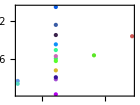

```mathematica
Normal[datagrouped[["human",All,{"Expected_frequency","Frequency","Change"}]]];
Graphics[Flatten[{legend[#Change],Point[{#["Expected_frequency"],#["Frequency"]}]}&/@%],Frame->True,AspectRatio->3/4]
```

```mathematica
Values@Normal[datagrouped[["human",All,{"Expected_frequency","Frequency"}]]]
```

{{0.0606061,0.142487},{0.0606061,0.0977979},{0.030303,0.0246114},{0.121212,0.0958549},{0.0909091,0.0654145},{0.030303,0.0200777},{0.0606061,0.0272021},{0.0606061,0.0602332},{0.0606061,0.0563472},{0.0606061,0.0829016},{0.0606061,0.11399},{0.0606061,0.0738342},{0.0606061,0.0641192},{0.0606061,0.0414508},{0.0606061,0.0304404},{0.0606061,0.00323834}}

```mathematica
Black
```

```mathematica
GrayLevel[0]
```

```mathematica
coloredAmino1=<|"KR"->RGBColor[0.010563313554859288, 0.842598209242611, 0.28387676305890275],"SG"->RGBColor[0.27953532144977733, 0.4836435395506147, 0.42893085600422864],"IM"->RGBColor[0.550447550119203, 0.1376882171135425, 0.10417086466364123],"TA"->RGBColor[0.5007397164248966, 0.7840482366236328, 0.7045968561167071],"IV"->RGBColor[0.2073047547900564, 0.09766618304217212, 0.7900750170440545],"MV"->RGBColor[0.7368627516800415, 0.9854810528894713, 0.16876607015856604],"HR"->RGBColor[0.6257486253643563, 0.18583347602533107, 0.08319093382232734],"NS"->RGBColor[0.9619547743747547, 0.5741162790544341, 0.1898822938015785],"ND"->RGBColor[0.2786813860224029, 0.8446411358513435, 0.5682812147647314],"QR"->RGBColor[0.7161778051845769, 0.7079120059790731, 0.8547544010382961],"KE"->RGBColor[0.9204697991268052, 0.01247026853391442, 0.588547608246031],"EG"->RGBColor[0.5494103924690645, 0.28378601201396725, 0.9354421828064061],"RG"->RGBColor[0.7039543181525214, 0.4665112553665334, 0.9831352427359885],"YC"->RGBColor[0.5185946438295199, 0.3923872911409534, 0.20838843032037646],"DG"->RGBColor[0.965242919857114, 0.6592751425902181, 0.052085256107477385],"stop-W"->RGBColor[0.5034569251580197, 0.09809664422436004, 0.7443255369657586]|>;
```

```mathematica
legend1=SwatchLegend[Values@coloredAmino1,Keys@coloredAmino1,LegendLabel->"Aminoacids changes",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5]
```

```mathematica
coloredAmino=<|"KR"->RGBColor[0.010563313554859288, 0.842598209242611, 0.28387676305890275],"SG"->RGBColor[0.27953532144977733, 0.4836435395506147, 0.42893085600422864],"IM"->RGBColor[0.550447550119203, 0.1376882171135425, 0.10417086466364123],"TA"->RGBColor[0.5007397164248966, 0.7840482366236328, 0.7045968561167071],"IV"->RGBColor[0.2073047547900564, 0.09766618304217212, 0.7900750170440545],"syn"-> GrayLevel[0],"MV"->RGBColor[0.7368627516800415, 0.9854810528894713, 0.16876607015856604],"HR"->RGBColor[0.6257486253643563, 0.18583347602533107, 0.08319093382232734],"NS"->RGBColor[0.9619547743747547, 0.5741162790544341, 0.1898822938015785],"ND"->RGBColor[0.2786813860224029, 0.8446411358513435, 0.5682812147647314],"QR"->RGBColor[0.7161778051845769, 0.7079120059790731, 0.8547544010382961],"KE"->RGBColor[0.9204697991268052, 0.01247026853391442, 0.588547608246031],"EG"->RGBColor[0.5494103924690645, 0.28378601201396725, 0.9354421828064061],"RG"->RGBColor[0.7039543181525214, 0.4665112553665334, 0.9831352427359885],"YC"->RGBColor[0.5185946438295199, 0.3923872911409534, 0.20838843032037646],"DG"->RGBColor[0.965242919857114, 0.6592751425902181, 0.052085256107477385],"stop-W"->RGBColor[0.5034569251580197, 0.09809664422436004, 0.7443255369657586]|>;
```

```mathematica
legend=SwatchLegend[Values@coloredAmino,Keys@coloredAmino,LegendLabel->"Aminoacids changes",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5]
```

```mathematica
rulesTicks=MapIndexed[#1->First[#2]&,{"KR","SG","IM","TA","IV","MV","HR","NS","ND","QR","KE","EG","RG","YC","DG","stop-W","syn"}]
```

{KR→1,SG→2,IM→3,TA→4,IV→5,MV→6,HR→7,NS→8,ND→9,QR→10,KE→11,EG→12,RG→13,YC→14,DG→15,stop-W→16,syn→17}

```mathematica
rulesColors={_String->Blue}
```

{_String→RGBColor[0, 0, 1]}

```mathematica
rules=Join[rulesTicks,rulesColors]
```

{KR→1,SG→2,IM→3,TA→4,IV→5,MV→6,HR→7,NS→8,ND→9,QR→10,KE→11,EG→12,RG→13,YC→14,DG→15,stop-W→16,syn→17,_String→RGBColor[0, 0, 1]}

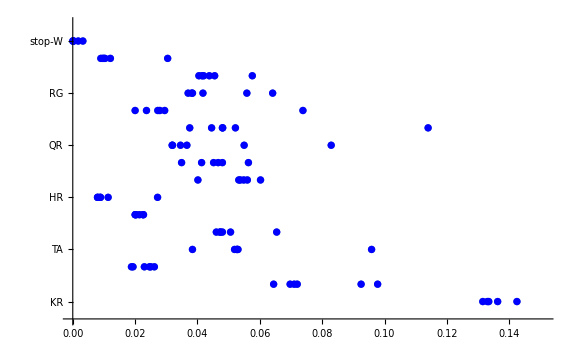

```mathematica
ListPlot[
MapThread[Style[{#2,#1},#3]&,Transpose@Values[Normal[data[All,{"Change","Frequency","Species"}]]]/.rules],
Ticks->{Automatic,Transpose@{Values[rulesTicks],Keys[rulesTicks]}},
ImageSize->Large]
```

```mathematica
Normal@Keys@datagrouped
```

{human,specific_sepia,conserved_cephalopods,specific_oct_bim,specific_squid,specific_oct_vul}

```mathematica
Table[ListPlot[
MapThread[Style[#1,Values[#2]]&,{Values@Normal[datagrouped[[species,All,{"Expected_frequency","Frequency"}]]],Normal@coloredAmino}],
PlotLegends->legend,
PlotStyle->PointSize[0.02],
ImageSize->Large
],{species,{"specific_sepia","conserved_cephalopods","specific_oct_bim","specific_squid","specific_oct_vul"}}
```

Join, TabView

```mathematica
Table[
ListPlot[
MapThread[Style[#1,Values[#2]]&,{Values@Normal[datagrouped[[species,All,{"Expected_frequency","Frequency"}]]],Normal@coloredAmino}],
PlotLegends->legend,
PlotStyle->PointSize[0.02],
ImageSize->Large],{species,{"specific_sepia","conserved_cephalopods","specific_oct_bim","specific_squid","specific_oct_vul"}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TabView[
Table[
ListPlot[
MapThread[Style[#1,Values[#2]]&,{Values@Normal[datagrouped[[species,All,{"Expected_frequency","Frequency"}]]],Normal@coloredAmino}],
PlotLegends->legend,
PlotStyle->PointSize[0.02],
ImageSize->Large],{species,{"specific_sepia","conserved_cephalopods","specific_oct_bim","specific_squid","specific_oct_vul"}}]
,
ListPlot[
MapThread[Style[#1,Values[#2]]&,{Values@Normal[datagrouped[["human",All,{"Expected_frequency","Frequency"}]]],Normal@coloredAmino1}],
PlotLegends->legend1,
PlotStyle->PointSize[0.02],
ImageSize->Large
]]
```

12345

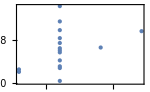

```mathematica
ListPlot[datagrouped[["human",All,{"Expected_frequency","Frequency"}]],PlotStyle->PointSize[Medium],Frame->True]
```

```mathematica
(*LEGEND:    StackedListPlot[PercentWorldGDP,PlotTheme->"Marketing",PlotLegends->{"Western Europe","Eastern Europe","Former USSR","Western Offshoots","Latin America","Japan","Asia","Africa"},ImageSize->300,FrameLabel->{"Year","% of World GDP"},PlotMarkers->None]   *)
```

```mathematica
aList={{1,1},{2,3},{4,5},{6,7}};
colorList={Black,Red,Blue,Yellow};
bList={#}&/@aList;
ListPlot[bList,PlotStyle->colorList]
```

```mathematica
LineLegend[ColorData[97]/@{1,2,3},{Sin[x],Cos[y],Tan[z]}]
```

```mathematica
PlotLegends -> data[[All,"Change"]],PlotStyle->PointSize[Medium],AxesLabel->Automatic
color=change,PlotLegends->{0.3,0.5,0.8} PlotTheme->"Scientific"
```

```mathematica
Graphics[Point[{Normal[datagrouped[["human",All,{"Frequency","Change"}]]]["Change"],Normal[datagrouped[["human",All,{"Frequency","Change"}]]]["Frequency"]}]];
```

```mathematica
datagrouped[["human",All,{"Frequency","Change"}]] ;
```

```mathematica
Normal[datagrouped[["human",All,{"Expected_frequency","Frequency","Change"}]]];
Graphics[Flatten[{legend[#Change],Point[{#["Expected_frequency"],#["Frequency"]}]}&/@%],Frame->True,AspectRatio->3/4]
```

```mathematica
BoxWhiskerChart
```